```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Desktop/Physics/PhD/DY/NNLO/rr/INTEGRATE/IF1

```mathematica
GetEnvironment["PATH"][[2]]
SetEnvironment["PATH"->GetEnvironment["PATH"][[2]]<>":/usr/local/bin"]
<<PolyLogTools`
$HPLAutoConvertToKnownFunctions = True
```

/usr/bin:/bin:/usr/sbin:/sbin

(****** PolyLogTools 1.3 ******)

Authors: Claude Duhr, Falko Dulat

Emails: claude.duhr@cern.ch, dulatf@slac.stanford.edu

PolyLogTools uses the implementation of the PSLQ algorithm by P. Bertok (http://library.wolfram.com/infocenter/MathSource/4263/)

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set for + - weights loaded for weights: <>StringTake[,{1,-3}]<>.

Table of MZVs loaded up to weight Null

Table of values at I loaded up to weight Null

Get::stream: ToFileName[{$HPLPath},nmzv.m] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

True

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Wed 2 Apr 2025 00:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

## Integral family definition (run this)

```mathematica
SetDim[d];
Declare[
{p1,p2,p4,p5},Vector,
{z,u,m2},Number];
(* kinematics *)
q=p1+p2-p4-p5;
sp[p1,p1]=0;
sp[p2,p2]=0;
sp[p1,p2]=m2/(2z);
```

```mathematica
fam = "IF1";
Get[NotebookDirectory[]<>"FamRed/"<>fam<>"/"<>fam];
MIs[IF1]
tomis = {};
Mdlog=Import["../AllDlogs/CanonicalBasisAll/"<>fam<>"/MdlogRatioIndep.m"];
basis = Import["./canDeq/basis.m"];
```

{j[IF1,1,1,1,1,0,0,0],j[IF1,2,1,1,1,0,0,0],j[IF1,1,1,1,1,0,0,1],j[IF1,1,1,1,1,0,1,0],j[IF1,1,1,1,1,0,1,1],j[IF1,1,1,1,1,1,1,1]}

```mathematica
(*the following extract the soft behaviour from a long list of integrals. It is used then to find relations from consistency conditions, in extrasoftrules*)
softrepl=Import["../DenAnalysis/softReplAll.m"];
extrasoftrules=Import["../DenAnalysis/soft_extra_rules.m"];
formsAll = Import["../AllDlogs/CanonicalBasisAll/dlogsAll.m"];
rules = Import["../AllDlogs/dlogIndependent.m"];
combineRule = Import["../AllDlogs/combinerules.m"];
replacementSoft = Import["../AllDlogs/SoftRegRules.m"];
formsName=Thread[Rule[formsAll[[]], Table[l[i], {i,1,29}]]];
RevformsName=Thread[Rule[formsName[[;;,2]],formsName[[;;,1]]]];
toZY  ={Kp->(r+t)(1 + r t), Km->(r-t)(1 - r t) , r-> Sqrt[u], t-> Sqrt[z], u->(y+z-y z)/(1-y+y z), z-> 1-bz}
```

{Kp→(r+t) (1+r t),Km→(r-t) (1-r t),r→√u,t→√z,u→(y+z-y z)/(1-y+y z),z→1-bz}

## phase space

```mathematica
SetAttributes[SP, Orderless]
SP[a_+b_,c_]:= SP[a,c]+SP[b,c]
SP[a_,-b_]:=- SP[a,b]
physKin = {SP[p4,p4]-> 0,SP[p5,p5]-> 0, SP[p1,p1]-> 0, SP[p1,p2] ->  m2/2/z, SP[p2,p2]-> 0}
InitalKin = { SP[p1,p1]-> 0, SP[p1,p2] ->  m2/2/z, SP[p2,p2]-> 0};
```

{SP[p4,p4]→0,SP[p5,p5]→0,SP[p1,p1]→0,SP[p1,p2]→m2/(2 z),SP[p2,p2]→0}

```mathematica
NormEp=Sep -> E^(EulerGamma ep)/(4 Pi)^ep;
Ω[n_] := (2 π^(n/2))/Gamma[n/2];
```

```mathematica
toZY  ={Kp->(r+t)(1 + r t), Km->(r-t)(1 - r t) , r-> Sqrt[u], t-> Sqrt[z], u->(y+z-y z)/(1-y+y z), z-> 1-bz};
y2u=y -> (-u+z)/((1+u) (-1+z));
```

```mathematica
NN =Norm -> Omega[d-2]Omega[d-3] ((1-y) y)^(1-2 eps)(bz)^(2-4 eps)/2^(4 + 2 eps) E^(EulerGamma 2 eps) /Pi^(d-2);
```

```mathematica
(*s2h -> (p2-q)^2*)
ss={s2h ->-(1-y)(1-z)(1-λ1(r-t)/r/(1+r t)), s1h -> - y (1-z)(1-λ1 r (1 -r t )/(r+t)), s24->-λ2 y (1-z)(1+λ1(1- r t )/r/(r+t)) ,s25->-(1-λ2) y (1-z)(1+λ1(1- r t )/r/(r+t)) ,s45 ->λ1 y (1-y)(1-z)^2 (1+u)^2/Kp/r,s14->-(1-y)(1-z)/(Kp r (1+λ1(1-r t )/r/(r+t)))(A1 +A2 + 2 (2 λ4 -1)Sqrt[A1 A2]), A1 ->λ1(1-λ2)(1+u)^2, A2 ->λ2 (1-λ1)r (Kp-λ1 Km),s15 ->s2h -s14 +s45 }
p2dotq=((-z+s2h)/2 //. ss /.(r-t) ->Km /(1-r t)/. 1/(1-r t) /(1+r t)-> 1/(1- z u)/.Km λ1-> TMP r (1+z)/.y2u//Simplify//Factor)/.(-1+TMP)-> 1-(Km λ1)/(r (1+z));
```

{s2h→(-1+y) (1-z) (1-((r-t) λ1)/(r (1+r t))),s1h→-y (1-z) (1-(r (1-r t) λ1)/(r+t)),s24→-y (1-z) (1+((1-r t) λ1)/(r (r+t))) λ2,s25→y (1-z) (1+((1-r t) λ1)/(r (r+t))) (-1+λ2),s45→((1+u)^2 (1-y) y (1-z)^2 λ1)/(Kp r),s14→((-1+y) (1-z) (A1+A2+2 √(A1 A2) (-1+2 λ4)))/(Kp r (1+((1-r t) λ1)/(r (r+t)))),A1→(1+u)^2 λ1 (1-λ2),A2→r (1-λ1) (Kp-Km λ1) λ2,s15→-s14+s2h+s45}

### The first soft master is INT[1,1,1,1,0,0,0], is INTEGRAND/(p2.q), because of the different delta. (1-z)^(2-4eps). ALSO, s -> m2/z and then m2-> 1 FFS

```mathematica
(*this is the scalar integrand, the second factor comes from the reconversion of the jacobian*)
INTEGRAND=((1+z)/(1+u)^2 )Norm ((Kp r)/(1+u)^2)^(-1+eps) ((1-λ1) (1-(Km λ1)/Kp))^-eps (1-(Km λ1)/(r (1+z))) (λ1 (1-λ2) λ2)^-eps ((1-λ4) λ4)^(-1/2-eps) ;
```

```mathematica
(*result to print 
2^-d  ⅇ^(2 eps EulerGamma) π^(2-d)  Omega[-2+d] Omega[-1+d]    z^(2 eps)1/(1+u)^(1-2 eps)((u-z)(1-u z))^(1- 2 eps)/(√u (√u+√z) (1+√u √z))^(1-eps) K[0]*)
```

```mathematica
(((u-z)(1- u z ))//.toZY//Simplify)
(1/(1+u)//.toZY//Simplify)
```

-((-2+bz)^2 bz^2 (-1+y) y)/(-1+bz y)^2

(-1+bz y)/(-2+bz)

```mathematica
(((-2+bz)^2/(-1+bz y)^2)^(-eps) ((-1+bz y)/(-2+bz))^(1-2 eps)//PowerExpand // FullSimplify)/.bz -> 1-z//FullSimplify
```

(1+y (-1+z))/(1+z)

```mathematica
D[(y+z-y z)/(1-y+y z),y]//FullSimplify
```

(1-z^2)/(1+y (-1+z))^2

```mathematica
(1+y (-1+z))/(1+z)(1-z^2)/(1+y (-1+z))^2//FullSimplify
```

(1-z)/(1+y (-1+z))

```mathematica
INTEGRAND/ p2dotq 
Series[1/p2dotq //. toZY, {y,0,-1}]
Series[1/p2dotq //. toZY, {y,1,-1}]
```

(2 Norm ((Kp r)/(1+u)^2)^(-1+eps) ((1-λ1) (1-(Km λ1)/Kp))^-eps (λ1 (1-λ2) λ2)^-eps ((1-λ4) λ4)^(-1/2-eps))/(1+u)

O[y]^0

O[y-1]^0

```mathematica
I0= (1/z)^(-2 eps)INTEGRAND/p2dotq;
Series[I0//.ss//.toZY,{bz,0,-2}]
tmp=Integrate[Integrate[I0/.ss, {λ4,0,1}],{λ2,0,1}][[1]]
(*no extra suppression in bz*)
tmp2=Series[tmp//.toZY,{bz,0,0}]//Normal
final=Integrate[tmp2, {λ1,0,1}][[1]]
```

O[bz]^0

(2^(1+4 eps) Norm π ((Kp r)/(1+u)^2)^(-1+eps) (1/z)^(-2 eps) λ1^-eps (((-1+λ1) (-Kp+Km λ1))/Kp)^-eps)/((1-2 eps) (1+u))

(2^(4 eps) Norm π (1-λ1)^-eps λ1^-eps)/(1-2 eps)

(16^eps Norm π Gamma[1-eps]^2)/((1-2 eps) Gamma[2-2 eps])

```mathematica
tmp
```

(2^(1+4 eps) Norm π ((Kp r)/(1+u)^2)^(-1+eps) (1/z)^(-2 eps) λ1^-eps (((-1+λ1) (-Kp+Km λ1))/Kp)^-eps)/((1-2 eps) (1+u))

```mathematica
Omega[-3+d] Omega[-2+d]/( Omega[-2+d] Omega[-1+d])/. Omega ->Ω/. d-> 4 -2 eps//FullSimplify
```

(1-2 eps)/(2 π)

```mathematica
(2^(-3+2 eps)  ⅇ^(2 eps EulerGamma) π^(2-d)  Omega[-3+d] Omega[-2+d] π   z^(2 eps))/(1-2 eps)
```

(2^(-3+2 eps) ⅇ^(2 eps EulerGamma) π^(3-d) z^(2 eps) Omega[-3+d] Omega[-2+d])/(1-2 eps)

```mathematica
/(bz^2)/ ((1-y) y) //.toZY// Simplify
```

```mathematica
toZY
```

{Kp→(r+t) (1+r t),Km→(r-t) (1-r t),r→√u,t→√z,u→(y+z-y z)/(1-y+y z),z→1-bz}

```mathematica
Solve[(y+z-y z)/(1-y+y z)== u,y]
```

{{y→(-u+z)/(-1-u+z+u z)}}

```mathematica
((-1+bz y)^2/(-2+bz)^2)^(1-2 eps)/.bz -> 1-z/.y->(-u+z)/(-1-u+z+u z)//Simplify
```

(1/(1+u)^2)^(1-2 eps)

```mathematica
NN
```

Norm→2^(-4-2 eps) bz^(2-4 eps) ⅇ^(2 eps EulerGamma) π^(2-d) ((1-y) y)^(1-2 eps) Omega[-3+d] Omega[-2+d]

```mathematica
(*final=(16^eps Norm π Gamma[1-eps]^2)/((1-2 eps) Gamma[2-2 eps]);*)
```

```mathematica
(*Leading behavior in bz*)
(* final=bz^(2-4 eps)((1-y) y)^(1-2 eps)(final/ bz^(2-4 eps) /((1-y) y)^(1-2 eps) /.NN/.d-> 4 -2 eps/.Omega-> Ω//FullSimplify)
Collect[final/.bz^a_->P[bz,a], {_P},FF] /. FF[a__]->1 /. P[bz,a__]->bz^a *)
```

```mathematica
(*this is the first master in the soft limit*)
(*toexpand=final/.bz^a_ :> P[bz,a]/.((1-y) y)^b_ :> P2[(1-y)y,b] /. P[a__,b__]:> P[a,b /. eps-> epps]/. P2[a__,b__]:> P2[a,b /. eps-> epps]*)
```

```mathematica
(*fact=((1- u z )(u-z)/.toZY/.bz-> 1-z//FullSimplify)^(2) ((1-y) y)^-2(1-z)^(-4)//FullSimplify;*)
```

```mathematica
(*Series[final bz^(4 eps) ((1-y) y)^(2 eps) fact^(eps)  /. z-> 1-bz, {bz,0,2}]//Normal*)
```

```mathematica
(*HB = P[bz,2-4 epps] P2[(1-y) y,1-2 epps];
Soft1=Collect[Series[toexpand/HB, {eps,0,6}],{_P2,_P,eps}];
Soft1 = Collect[Collect[Soft1/.PolyGamma[0,3/2]->(2-EulerGamma-Log[4]),{eps,π^6},Simplify],{eps},Factor];
coeffs=Collect[CoefficientList[Soft1,eps],{_Log},FullSimplify];
coeffs=coeffs//FullSimplify
*)
```

```mathematica
(*Export["./SoftMasters/m1_1111000.m",{HB,coeffs}//Cancel]
Export["./SoftMasters/Fm1_1111000.m",HB * {1,eps, eps^2,eps^3,eps^4,eps^5,eps^6}.coeffs]*)
```

## Boundaries

#### soft reduction

```mathematica
LRbasis=MIs[IF1];
myLaporta=MIs[IF1]/.j[IF1,2,1,1,1,0,0,0]->j[IF1,1,1,1,1,-1,0,0];
tomis=ToMIsRule[myLaporta];
Put[myLaporta,"IF1/Mi"]
```

```mathematica
IBPReduce[basis]
```

{-((-3+d) (-10+3 d) √u j[IF1,1,1,1,1,0,0,0])/(8 m2 √z)-((-4+d) √u (1+z) j[IF1,2,1,1,1,0,0,0])/(8 z^(3/2)),((-4+d) (1+u) j[IF1,2,1,1,1,0,0,0])/(4 z),-((-4+d)^2 u j[IF1,1,1,1,1,0,0,1])/(2 m2 z)+((-4+d) (1+u) j[IF1,2,1,1,1,0,0,0])/(m2 z),-((-4+d)^2 j[IF1,1,1,1,1,0,1,0])/(2 z),-((-4+d)^2 √u j[IF1,1,1,1,1,0,1,1])/(2 z^(3/2)),-((-4+d)^2 j[IF1,1,1,1,1,0,1,1])/(2 z^2)+((-4+d)^2 (-1+u z) j[IF1,1,1,1,1,1,1,1])/(2 z^3)}

```mathematica
(*first find order*)
order=-Exponent[(Oser=Series[bz^(4eps)IBPReduce[basis]/.tomis /.softrepl/.extrasoftrules//.toZY /. y-> 1/3 /. d-> -10/.m2-> 3, {bz, 0,2}] //Normal )/. bz -> 1/bz,bz]
orderCheck=-Exponent[(Oser=Series[bz^(4eps)IBPReduce[basis]/.tomis /.softrepl/.extrasoftrules//.toZY /. y-> 1/7 /. d-> -5/.m2-> 2, {bz, 0,2}] //Normal )/. bz -> 1/bz,bz];
If[orderCheck === order, Print["All Good"], Print["AHHH  something wrong in determination lowest order in the soft expansion"]]
```

{0,0,0,1,0,0}

All Good

```mathematica
tmp=bz^(4eps)IBPReduce[basis]/.tomis /.softrepl/.extrasoftrules//.toZY;
ser={};
Do[ser=Append[ser,Series[tmp[[i]] , {bz, 0,order[[i]]}]]/.m2-> 1//Normal, {i,1,Length[basis]}]
ser=Collect[ser, {_j}, Together]
```

{-((-3+d)^2 j[IF1soft,1,1,1,1,0,0,0])/(2 (-1+y) y),((-3+d)^2 j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y),(4 (-3+d)^2 j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y),(bz (-4+d) (-3+d) j[IF1soft,1,1,1,1,0,0,0])/y,(2 (9-6 d+d^2) j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y),(2 (9-6 d+d^2) j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y)+(-4+d)^2 (-1+y) j[IF1soft,1,1,1,1,1,1,1]}

#### Eigenavlues condition for last master

```mathematica
Length[formsAll]
```

29

```mathematica
toZY
Series[formsAll/.Log[a__]-> a//.toZY, {bz,0,-2}];
Series[D[Series[Log@(Series[formsAll/.Log[a__]-> a//.toZY, {bz,0,1}]//Normal), {bz,0,2}]  ,bz], {bz,0,-1}]//Normal;
leadingBZforms=Thread[Rule[formsAll,%]]
```

{Kp→(r+t) (1+r t),Km→(r-t) (1-r t),r→√u,t→√z,u→(y+z-y z)/(1-y+y z),z→1-bz}

{Log[z]→0,Log[u]→0,Log[1-z]→1/bz,Log[1-u]→1/bz,Log[1+z]→0,Log[1+u]→0,Log[u-z]→1/bz,Log[1-u z]→1/bz,Log[(√u-√z)/(√u+√z)]→1/bz,Log[(1-√u √z)/(1+√u √z)]→1/bz,Log[u^2 (-4+z)+z+2 u z]→1/bz,Log[1+4 (1+u) z]→0,Log[u+4 (1+u) z]→0,Log[4-(1+u)^2 z]→1/bz,Log[(1-ⅈ √z)/(1+ⅈ √z)]→0,Log[(1-ⅈ √u)/(1+ⅈ √u)]→0,Log[(1-√(u/(1+u)))/(1+√(u/(1+u)))]→0,Log[(√u-2 √z-√(u+4 z+4 u z))/(√u+2 √z-√(u+4 z+4 u z))]→-1/bz,Log[(√u-√(u+4 z+4 u z))/(√u+√(u+4 z+4 u z))]→0,Log[(√u-2 √z+√(u+4 z+4 u z))/(√u+2 √z-√(u+4 z+4 u z))]→-1/bz,Log[(1-√(1+4 (1+u) z))/(1+√(1+4 (1+u) z))]→0,Log[(1+2 u-√(1+4 (1+u) z))/(1+2 u+√(1+4 (1+u) z))]→1/bz,Log[(1+2 u+2 √u √(1+u)+2 √(1+u) √z-√(1+4 (1+u) z))/(-1-2 u+2 √u √(1+u)-2 √(1+u) √z+√(1+4 (1+u) z))]→-1/bz,Log[-((1+u) √z-ⅈ √(4 u^2-(1+u)^2 z))/(2 u)]→0,Log[1/2 ((1+u) √z+ⅈ √(4-(1+u)^2 z))]→0,Log[(-√u+u^(3/2)-ⅈ √(4 u^2-(1+u)^2 z))/(-√u+u^(3/2)+ⅈ √(4 u^2-(1+u)^2 z))]→0,Log[(1-u+ⅈ √u √(4-(1+u)^2 z))/(1-u-ⅈ √u √(4-(1+u)^2 z))]→0,Log[(u (-2+z)+z-ⅈ √z √(4 u^2-(1+u)^2 z))/(2 √u √(u-z))]→0,Log[(-2+z+u z+ⅈ √z √(4-(1+u)^2 z))/(2 √(1-u z))]→0}

```mathematica
formsSoftReg= Union@Cases[formsAll /. replacementSoft, Log[a__], Infinity];
Series[formsSoftReg/.Log[a__]-> a//.toZY, {bz,0,-2}];
Series[D[Series[Log@(Series[formsSoftReg/.Log[a__]-> a//.toZY, {bz,0,1}]//Normal), {bz,0,2}]  ,bz], {bz,0,-1}]//Normal;
leadingBZforms=Thread[Rule[formsSoftReg,%]];
```

```mathematica
MdlogSoftReg=Collect[Mdlog /. replacementSoft, {_Log}, Together];
```

```mathematica
dbzLeading=MdlogSoftReg/. leadingBZforms;
LeadingMatrixBZ=MatrixExp[Coefficient[(dbzLeading),1/bz]Log[bz]eps];
```

```mathematica
tmprule=Solve[ser[[6]]== soft6, j[IF1soft,1,1,1,1,1,1,1]]//Simplify//Flatten;
-4 eps /bz ( ser[[6]] /.bz-> 0)/. d-> 4 -2 eps/.tmprule/. d-> 4 -2 eps;
Series[eps(dbzLeading[[]].(ser/.bz-> 0))[[6]]//Simplify, {bz,0,-1}]/.d-> 4 -2 eps/.tmprule/.d-> 4 -2 eps//Normal;
toprule=Collect[Solve[%%-%==0,soft6][[1]], {_j}, Together]
```

{soft6→-(6 (1-4 eps+4 eps^2) j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y)}

```mathematica
Ser=ser /. tmprule/. toprule//Simplify;
```

## Fix boundaries === Soft Int

```mathematica
mSoft = Import["./SoftMasters/m1_1111000.m"];
FmSoft = Import["./SoftMasters/Fm1_1111000.m"];
prefy=Cases[mSoft[[1]], P2[a__]][[1]] /. P2[a_,b_]-> a^b /. epps -> eps;
prefz=Cases[mSoft[[1]], P[a__]][[1]] /. P[a_,b_]-> a^b /. epps -> eps;
```

```mathematica
MSOFT=(FmSoft /. P[a__]-> 1 /. P2[a_,b_]-> a^b /. epps -> eps);
const=Collect[Series[(Ser /. d-> 4 -2 eps /. bz -> 0 /.j[IF1soft,1,1,1,1,0,0,0]-> MSOFT  (-((-2+bz)^2  (-1+y) y)/(-1+bz y)^2)^(2 eps)/.bz-> 0/. y-> 1/2), {eps,0,6}]//Normal, {eps}, FullSimplify];
```

```mathematica
-(6 (1-2 eps)^2 j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y)  (-((-2+bz)^2  (-1+y) y)/(-1+bz y)^2)^(2 eps)
```

-(6 (1-2 eps)^2 (-((-2+bz)^2 (-1+y) y)/(-1+bz y)^2)^(2 eps) j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y)

```mathematica
Ser
```

{-((-3+d)^2 j[IF1soft,1,1,1,1,0,0,0])/(2 (-1+y) y),((-3+d)^2 j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y),(4 (-3+d)^2 j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y),(bz (-4+d) (-3+d) j[IF1soft,1,1,1,1,0,0,0])/y,(2 (-3+d)^2 j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y),-(6 (1-2 eps)^2 j[IF1soft,1,1,1,1,0,0,0])/((-1+y) y)}

```mathematica
(*Export["./CONST/const.m",const]*)
```

```mathematica
dlogToadd=2 eps (Log[u-z]+Log[-1+u z]) IdentityMatrix[6] /. eps -> 1 /. Log[u-z] -> Log[u] +  Log[1+(√z)/(√u)] + Log[1-(√z)/(√u)]/.Log[-1+u z]-> Log[1-√u √z]+Log[1+√u √z]
```

{{2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0,0,0,0},{0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0,0,0},{0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0,0},{0,0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0},{0,0,0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0},{0,0,0,0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z])}}

## Collinear limit y -> 0 (u -> z) (Rules are for formsAll)

```mathematica
collLimit0=Import["../AllDlogs/Coll0.m"];
collinearLogs=Import["../AllDlogs/collinear_logs.m"]
collinearLogs // Length
collinearName = Thread[Rule[collinearLogs, Table[cl[i], {i,1,Length[collinearLogs]}]]];
revcollinearName=Thread[Rule[collinearName[[;;,2]],collinearName[[;;,1]]]]
```

{Log[-(ⅈ+√z)/(-ⅈ+√z)],Log[1-z],Log[z],Log[1+z],Log[1+2 z],Log[5+4 z],Log[2+z+2 √(1+z)],Log[1+2 z-2 √z √(1+z)],Log[4-z (1+z)^2],Log[1+√(5+4 z)],Log[2+z+√(5+4 z)],Log[1/2 (√z (1+z)+ⅈ √(4-z (1+z)^2))],Log[-2+z+z^2-ⅈ √z √(4-z (1+z)^2)]}

13

{cl[1]→Log[-(ⅈ+√z)/(-ⅈ+√z)],cl[2]→Log[1-z],cl[3]→Log[z],cl[4]→Log[1+z],cl[5]→Log[1+2 z],cl[6]→Log[5+4 z],cl[7]→Log[2+z+2 √(1+z)],cl[8]→Log[1+2 z-2 √z √(1+z)],cl[9]→Log[4-z (1+z)^2],cl[10]→Log[1+√(5+4 z)],cl[11]→Log[2+z+√(5+4 z)],cl[12]→Log[1/2 (√z (1+z)+ⅈ √(4-z (1+z)^2))],cl[13]→Log[-2+z+z^2-ⅈ √z √(4-z (1+z)^2)]}

```mathematica
TmpMdlog=Collect[Mdlog + dlogToadd/.combineRule/.rules, {_Log}, Together] /.collLimit0// Simplify;
MdlogY0=Collect[TmpMdlog , {_Log}, Together] /. collinearName;
Do[Y0AA[i]=Coefficient[MdlogY0   , cl[i]], {i,1,Length[collinearLogs]}];
Y0AA[Length[collinearLogs]+1]=Coefficient[MdlogY0, LogColl0];
formexp=Sum[AAA[i]cl[i], {i,1,Length[collinearLogs]+1}]/.cl[Length[collinearLogs]+1]-> LogColl0;
Y0Expansion[0]=IdentityMatrix[Length[basis]];
Y0Expansion[1] =formexp;
```

```mathematica
toadd1=Y0Expansion[0].Coefficient[const,eps,1] II[];
tmp1=Collect[(Y0Expansion[1]/. AAA-> Y0AA /. cl[a_]-> II[cl[a]]).Coefficient[const,eps,0], {_II},Together];
sol1IIy0 = tmp1 +toadd1 ;
ii=Union@Cases[tmp1, II[a__],Infinity];
letters = ii /. II-> List //Flatten ;
```

```mathematica
0
```

0

```mathematica
sol1IIy0/. II[a__]-> a /.revcollinearName/.z-> 1-bz
```

{1/2 II[] Log[2]+3/8 Log[1-bz]+3/8 Log[2-bz],-II[] Log[2]-3/4 Log[1-bz]-3/4 Log[2-bz],-2 II[] Log[4]-3 Log[1-bz]-3 Log[2-bz],Log[1-bz]-Log[2-bz],-II[] Log[4]-Log[1-bz]-2 Log[2-bz],II[] Log[64]+5 Log[1-bz]+4 Log[2-bz]}

```mathematica
(D[sol1IIy0/. II[a__]-> a  /. II[]-> 1/.revcollinearName/.z-> 1-bz,bz])
```

{-3/(8 (1-bz))-3/(8 (2-bz)),3/(4 (1-bz))+3/(4 (2-bz)),3/(1-bz)+3/(2-bz),-1/(1-bz)+1/(2-bz),1/(1-bz)+2/(2-bz),-5/(1-bz)-4/(2-bz)}

```mathematica
tmp=GIntegrate[#,bz]&/@(D[sol1IIy0/. II[a__]-> a  /. II[]-> 1/.revcollinearName/.z-> 1-bz,bz]);
solY0G1=tmp + toadd1 /. II[]-> 1;
```

```mathematica
toadd2=Y0Expansion[0].Coefficient[const,eps,2] II[];
tmp2=Collect[((Y0Expansion[1] /. AAA-> Y0AA).sol1IIy0//Expand) /. cl[a_]II[list___] -> II[list,cl[a]], {_II}, FullSimplify];
sol2IIy0 = tmp2 +toadd2;
ii=Union@Cases[tmp2, II[a__],Infinity];
ii /. II-> List // Flatten//Union
```

{cl[2],cl[3],cl[4]}

```mathematica
tmp=Collect[GIntegrate[#,bz]&/@(Collect[D[TmpMdlog /. z -> 1-bz,bz].solY0G1, {_G, _Log},Apart]), {_G}, FullSimplify];
solY0G2=tmp + toadd2 /.II[]-> 1;
```

```mathematica
toadd3=Y0Expansion[0].Coefficient[const,eps,3] II[];
tmp3=Collect[((Y0Expansion[1] /. AAA-> Y0AA).sol2IIy0//Expand) /. cl[a_]II[list___] -> II[list,cl[a]], {_II}, FullSimplify];
sol3IIy0 = tmp3 +toadd3;
ii=Union@Cases[tmp3, II[a__],Infinity];
ii /. II-> List // Flatten//Union
```

{cl[2],cl[3],cl[4]}

```mathematica
tmp=Collect[GIntegrate[#,bz]&/@(Collect[D[TmpMdlog /. z -> 1-bz,bz].solY0G2, {_G, _Log},Apart]), {_G}, FullSimplify];
solY0G3=tmp + toadd3 /.II[]-> 1;
```

```mathematica
toadd4=Y0Expansion[0].Coefficient[const,eps,4] II[];
tmp4=Collect[((Y0Expansion[1] /. AAA-> Y0AA).sol3IIy0//Expand) /. cl[a_]II[list___] -> II[list,cl[a]], {_II}, FullSimplify];
sol4IIy0 = tmp4 +toadd4;
ii=Union@Cases[tmp4, II[a__],Infinity];
ii /. II-> List // Flatten//Union
```

{cl[2],cl[3],cl[4]}

```mathematica
tmp=Collect[GIntegrate[#,bz]&/@(Collect[D[TmpMdlog /. z -> 1-bz,bz].solY0G3, {_G, _Log},Apart]), {_G}, FullSimplify];
solY0G4=tmp + toadd4/.II[]-> 1;
(*gpls4 /. bz ->  0// Simplify*)
```

```mathematica
SOL0IIy0= Coefficient[const,eps,0]-II[]Coefficient[const,eps,0];
SOL1IIy0=Collect[ sol1IIy0-II[]Coefficient[const,eps,1], {_II}, Together];
SOL2IIy0= Collect[sol2IIy0-II[]Coefficient[const,eps,2], {_II}, Together];
SOL3IIy0=  Collect[sol3IIy0-II[]Coefficient[const,eps,3], {_II}, Together];
SOL4IIy0=  Collect[sol4IIy0-II[]Coefficient[const,eps,4], {_II}, Together];
```

```mathematica
Export["./SOLUTIONS/coll0/SOL0IIy0.m",SOL0IIy0]
Export["./SOLUTIONS/coll0/SOL1IIy0.m",SOL1IIy0]
Export["./SOLUTIONS/coll0/SOL2IIy0.m",SOL2IIy0]
Export["./SOLUTIONS/coll0/SOL3IIy0.m",SOL3IIy0]
Export["./SOLUTIONS/coll0/SOL4IIy0.m",SOL4IIy0]
```

./SOLUTIONS/coll0/SOL0IIy0.m

./SOLUTIONS/coll0/SOL1IIy0.m

./SOLUTIONS/coll0/SOL2IIy0.m

./SOLUTIONS/coll0/SOL3IIy0.m

./SOLUTIONS/coll0/SOL4IIy0.m

```mathematica
SOL0Gy0= Coefficient[const,eps,0]-Coefficient[const,eps,0];
SOL1Gy0=Collect[ solY0G1-Coefficient[const,eps,1], {_G}, Together];
SOL2Gy0= Collect[solY0G2-Coefficient[const,eps,2], {_G}, Together];
SOL3Gy0=  Collect[solY0G3-Coefficient[const,eps,3], {_G}, Together];
SOL4Gy0=  Collect[solY0G4-Coefficient[const,eps,4], {_G}, Together];
```

```mathematica
Export["./SOLUTIONS/coll0/SOL0Gy0.m",SOL0Gy0]
Export["./SOLUTIONS/coll0/SOL1Gy0.m",SOL1Gy0]
Export["./SOLUTIONS/coll0/SOL2Gy0.m",SOL2Gy0]
Export["./SOLUTIONS/coll0/SOL3Gy0.m",SOL3Gy0]
Export["./SOLUTIONS/coll0/SOL4Gy0.m",SOL4Gy0]
```

./SOLUTIONS/coll0/SOL0Gy0.m

./SOLUTIONS/coll0/SOL1Gy0.m

./SOLUTIONS/coll0/SOL2Gy0.m

./SOLUTIONS/coll0/SOL3Gy0.m

./SOLUTIONS/coll0/SOL4Gy0.m

## Collinear limit y -> 1 (u -> 1/z) (Rules are for formsAll)

```mathematica
collLimit1=Import["../AllDlogs/Coll1.m"];
collinearLogs=Import["../AllDlogs/collinear_logs.m"]
collinearLogs // Length
collinearName = Thread[Rule[collinearLogs, Table[cl[i], {i,1,Length[collinearLogs]}]]];
revcollinearName=Thread[Rule[collinearName[[;;,2]],collinearName[[;;,1]]]]
```

{Log[-(ⅈ+√z)/(-ⅈ+√z)],Log[1-z],Log[z],Log[1+z],Log[1+2 z],Log[5+4 z],Log[2+z+2 √(1+z)],Log[1+2 z-2 √z √(1+z)],Log[4-z (1+z)^2],Log[1+√(5+4 z)],Log[2+z+√(5+4 z)],Log[1/2 (√z (1+z)+ⅈ √(4-z (1+z)^2))],Log[-2+z+z^2-ⅈ √z √(4-z (1+z)^2)]}

13

{cl[1]→Log[-(ⅈ+√z)/(-ⅈ+√z)],cl[2]→Log[1-z],cl[3]→Log[z],cl[4]→Log[1+z],cl[5]→Log[1+2 z],cl[6]→Log[5+4 z],cl[7]→Log[2+z+2 √(1+z)],cl[8]→Log[1+2 z-2 √z √(1+z)],cl[9]→Log[4-z (1+z)^2],cl[10]→Log[1+√(5+4 z)],cl[11]→Log[2+z+√(5+4 z)],cl[12]→Log[1/2 (√z (1+z)+ⅈ √(4-z (1+z)^2))],cl[13]→Log[-2+z+z^2-ⅈ √z √(4-z (1+z)^2)]}

```mathematica
TmpMdlog=Collect[Mdlog + dlogToadd/.combineRule/.rules, {_Log}, Together] /.collLimit1// Simplify;
MdlogY1=Collect[TmpMdlog , {_Log}, Together] /. collinearName
Do[Y1AA[i]=Coefficient[MdlogY1   , cl[i]], {i,1,Length[collinearLogs]}]
Y1AA[Length[collinearLogs]+1]=Coefficient[MdlogY1, LogColl1]
formexp=Sum[AAA[i]cl[i], {i,1,Length[collinearLogs]+1}]/.cl[Length[collinearLogs]+1]-> LogColl1;
Y1Expansion[0]=IdentityMatrix[Length[basis]];
Y1Expansion[1] =formexp;
```

{{(3 LogColl1)/2+(3 cl[2])/2-cl[3]+(3 cl[4])/2,(3 LogColl1)/4+(3 cl[2])/4-(3 cl[4])/4,0,0,0,0},{LogColl1+cl[2]-cl[4],LogColl1/2+cl[2]/2-cl[3]+(5 cl[4])/2,0,0,0,0},{4 cl[2]-4 cl[4],-6 cl[2]+6 cl[4],2 cl[2]-2 cl[3]+2 cl[4],0,0,0},{-4 cl[2]+4 cl[4],-2 cl[2]+2 cl[4],0,2 LogColl1+2 cl[3],0,0},{0,-4 cl[2]+4 cl[4],-LogColl1,-cl[2]+cl[4],2 LogColl1+2 cl[2]-2 cl[3]+2 cl[4],0},{-8 cl[2]+8 cl[4],8 cl[2]-8 cl[4],-LogColl1-2 cl[3]+2 cl[4],-cl[2]+cl[4],2 LogColl1,2 cl[2]-2 cl[3]+2 cl[4]}}

{{3/2,3/4,0,0,0,0},{1,1/2,0,0,0,0},{0,0,0,0,0,0},{0,0,0,2,0,0},{0,0,-1,0,2,0},{0,0,-1,0,2,0}}

```mathematica
toadd1=Y1Expansion[0].Coefficient[const,eps,1]II[];
tmp1=Collect[(Y1Expansion[1]/. AAA-> Y1AA /. cl[a_]-> II[cl[a]]).Coefficient[const,eps,0], {_II},Together];
sol1IIy1 = tmp1 +toadd1;
ii=Union@Cases[tmp1, II[a__],Infinity];
letters = ii /. II-> List //Flatten
```

{cl[3],cl[4]}

```mathematica
tmp=GIntegrate[#,bz]&/@(D[sol1IIy1/. II[a__]-> a /.revcollinearName/.z-> 1-bz,bz]);
solY1G1=tmp + toadd1 /. II[]-> 1;
```

```mathematica
toadd2=Y1Expansion[0].Coefficient[const,eps,2] II[];
tmp2=Collect[((Y1Expansion[1] /. AAA-> Y1AA).sol1IIy1//Expand) /. cl[a_]II[list___] -> II[list,cl[a]], {_II}, FullSimplify];
sol2IIy1 = tmp2 +toadd2;
ii=Union@Cases[tmp2, II[a__],Infinity];
letters = ii /. II-> List //Flatten //Union
```

{cl[2],cl[3],cl[4]}

```mathematica
tmp=Collect[GIntegrate[#,bz]&/@(Collect[D[TmpMdlog /. z -> 1-bz,bz].solY1G1, {_G, _Log},Apart]), {_G}, FullSimplify];
solY1G2=tmp+ toadd2 /. II[]-> 1;
```

```mathematica
toadd3=Y1Expansion[0].Coefficient[const,eps,3] II[];
tmp3=Collect[((Y1Expansion[1] /. AAA-> Y1AA).sol2IIy1//Expand) /. cl[a_]II[list___] -> II[list,cl[a]], {_II}, FullSimplify];
sol3IIy1 = tmp3+toadd3;
ii=Union@Cases[tmp3, II[a__],Infinity];
letters = ii /. II-> List //Flatten //Union
```

{cl[2],cl[3],cl[4]}

```mathematica
tmp=Collect[GIntegrate[#,bz]&/@(Collect[D[TmpMdlog /. z -> 1-bz,bz].solY1G2, {_G, _Log},Apart]), {_G}, FullSimplify];
solY1G3= tmp+ toadd3 /. II[]-> 1;
```

```mathematica
toadd4=Y1Expansion[0].Coefficient[const,eps,4] II[];
tmp4=Collect[((Y1Expansion[1] /. AAA-> Y1AA).sol3IIy1//Expand) /. cl[a_]II[list___] -> II[list,cl[a]], {_II}, FullSimplify];
sol4IIy1 = tmp4+toadd4;
ii=Union@Cases[tmp4, II[a__],Infinity];
letters = ii /. II-> List //Flatten //Union
```

{cl[2],cl[3],cl[4]}

```mathematica
tmp=Collect[GIntegrate[#,bz]&/@(Collect[D[TmpMdlog /. z -> 1-bz,bz].solY1G3, {_G, _Log},Apart]), {_G}, FullSimplify];
solY1G4= tmp + toadd4 /. II[] -> 1;
```

```mathematica
SOL0IIy1= Coefficient[const,eps,0]-II[]Coefficient[const,eps,0];
SOL1IIy1=Collect[ sol1IIy1-II[]Coefficient[const,eps,1], {_II}, Together];
SOL2IIy1= Collect[sol2IIy1-II[]Coefficient[const,eps,2], {_II}, Together];
SOL3IIy1=  Collect[sol3IIy1-II[]Coefficient[const,eps,3], {_II}, Together];
SOL4IIy1=  Collect[sol4IIy1-II[]Coefficient[const,eps,4], {_II}, Together];
```

```mathematica
SOL0Gy1= Coefficient[const,eps,0]-Coefficient[const,eps,0];
SOL1Gy1=Collect[ solY1G1-Coefficient[const,eps,1], {_G}, Together];
SOL2Gy1= Collect[solY1G2-Coefficient[const,eps,2], {_G}, Together];
SOL3Gy1=  Collect[solY1G3-Coefficient[const,eps,3], {_G}, Together];
SOL4Gy1=  Collect[solY1G4-Coefficient[const,eps,4], {_G}, Together];
```

```mathematica
Export["./SOLUTIONS/coll1/SOL0IIy1.m",SOL0IIy1]
Export["./SOLUTIONS/coll1/SOL1IIy1.m",SOL1IIy1]
Export["./SOLUTIONS/coll1/SOL2IIy1.m",SOL2IIy1]
Export["./SOLUTIONS/coll1/SOL3IIy1.m",SOL3IIy1]
Export["./SOLUTIONS/coll1/SOL4IIy1.m",SOL4IIy1]
```

./SOLUTIONS/coll1/SOL0IIy1.m

./SOLUTIONS/coll1/SOL1IIy1.m

./SOLUTIONS/coll1/SOL2IIy1.m

./SOLUTIONS/coll1/SOL3IIy1.m

./SOLUTIONS/coll1/SOL4IIy1.m

```mathematica
Export["./SOLUTIONS/coll1/SOL0Gy1.m",SOL0Gy1]
Export["./SOLUTIONS/coll1/SOL1Gy1.m",SOL1Gy1]
Export["./SOLUTIONS/coll1/SOL2Gy1.m",SOL2Gy1]
Export["./SOLUTIONS/coll1/SOL3Gy1.m",SOL3Gy1]
Export["./SOLUTIONS/coll1/SOL4Gy1.m",SOL4Gy1]
```

./SOLUTIONS/coll1/SOL0Gy1.m

./SOLUTIONS/coll1/SOL1Gy1.m

./SOLUTIONS/coll1/SOL2Gy1.m

./SOLUTIONS/coll1/SOL3Gy1.m

./SOLUTIONS/coll1/SOL4Gy1.m

## Solution Hard

```mathematica
dlogToadd=2 eps (Log[u-z]+Log[-1+u z]) IdentityMatrix[6] /. eps -> 1 /. Log[u-z] -> Log[u] +  Log[1+(√z)/(√u)] + Log[1-(√z)/(√u)]/.Log[-1+u z]-> Log[1-√u √z]+Log[1+√u √z]
```

{{2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0,0,0,0},{0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0,0,0},{0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0,0},{0,0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0,0},{0,0,0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z]),0},{0,0,0,0,0,2 (Log[u]+Log[1-(√z)/(√u)]+Log[1+(√z)/(√u)]+Log[1-√u √z]+Log[1+√u √z])}}

```mathematica
SoftRegformsName = Import["../AllDlogs/CanonicalBasisAll/NAMEdlogAllReg.m"];
RevSoftRegformsName = Thread[Rule[SoftRegformsName[[;;,2]],SoftRegformsName[[;;,1]]]];
```

```mathematica
RegMdlog=Collect[Mdlog + dlogToadd/.combineRule/.rules/.replacementSoft, {_Log}, Together]/.SoftRegformsName;
Do[AA[i]=Coefficient[RegMdlog   /. SoftRegformsName, RSoftl[i]], {i,1,Length[SoftRegformsName]}]
formexp=Sum[AAA[i]RSoftl[i], {i,1,Length[SoftRegformsName]}];
Expansion[0]=IdentityMatrix[Length[basis]];
Expansion[1] =formexp;
```

```mathematica
sol0=Expansion[0].Coefficient[const,eps,0]
```

{1/8,-1/4,-1,0,-1/2,3/2}

```mathematica
toadd1=Expansion[0].Coefficient[const,eps,1]II[];
tmp1=Collect[(Expansion[1]/. AAA-> AA /. RSoftl[a_]-> II[RSoftl[a]]).Coefficient[const,eps,0], {_II},Together];
sol1II = tmp1 + toadd1 ;
ii=Union@Cases[tmp1, II[a__],Infinity];
letters = ii /. II-> List //Flatten ;
```

```mathematica
(*sol1reg=Import["./Solutions/Solutions_reg/Solution_reg_1.m"];*)
```

```mathematica
(*sol1reg=Import["./Solutions/Solutions_reg/Solution_reg_1.m"];
NIntegrate[(sol1II /. II[]-> 0) /. II[RSoftl[a_]]:>D[ RSoftl[a]/.RevSoftRegformsName//.toZY,bz]/.y-> 0.99,{bz,0,0.92}]+ Coefficient[sol1II, II[]];
Ginsh[#, {bz-> 0.92}]&/@(sol1reg //.toZY/.y-> 0.99);
%%-%
NIntegrate[(sol1II /. II[]-> 0) /. II[RSoftl[a_]]:>D[ RSoftl[a]/.RevSoftRegformsName//.toZY,bz]/.y-> 0.7,{bz,0,0.5}]+ Coefficient[sol1II, II[]];
Ginsh[#, {bz-> 0.5}]&/@(sol1reg //.toZY/.y-> 0.7);
%%-%*)
```

```mathematica
toadd2=Expansion[0].Coefficient[const,eps,2] II[];
tmp2=Collect[((Expansion[1] /. AAA-> AA).sol1II//Expand) /. RSoftl[a_]II[list___] -> II[list,RSoftl[a]], {_II}, FullSimplify];
sol2II = tmp2 + toadd2;
ii=Union@Cases[tmp2, II[a__],Infinity];
Union@Cases[ii, II[RSoftl[3], a__],Infinity]
letters = ii  /. II-> List// Flatten // Union
```

{}

{RSoftl[1],RSoftl[2],RSoftl[3],RSoftl[6],RSoftl[7],RSoftl[8],RSoftl[9],RSoftl[10]}

```mathematica
toadd3=Expansion[0].Coefficient[const,eps,3] II[];
tmp3=Collect[((Expansion[1] /. AAA-> AA).sol2II//Expand) /. RSoftl[a_]II[list___] -> II[list,RSoftl[a]], {_II}, FullSimplify];
sol3II = tmp3 + toadd3;
ii=Union@Cases[tmp3, II[a__],Infinity];
Union@Cases[ii, II[RSoftl[3], a__],Infinity]
letters = ii  /. II-> List// Flatten // Union
```

{}

{RSoftl[1],RSoftl[2],RSoftl[3],RSoftl[6],RSoftl[7],RSoftl[8],RSoftl[9],RSoftl[10]}

```mathematica
(*toadd4=Expansion[0].Coefficient[const,eps,4] II[];
tmp4=Collect[((Expansion[1] /. AAA-> AA).sol3II//Expand) /. RSoftl[a_]II[list___] -> II[list,RSoftl[a]], {_II}, FullSimplify];
sol4II = tmp4 + toadd4;
ii=Union@Cases[tmp4, II[a__],Infinity];
Union@Cases[ii, II[RSoftl[3], a__],Infinity]
letters = ii  /. II-> List// Flatten // Union*)
```

```mathematica
SOL0IIHard = sol0- sol0 - SOL0IIy0-SOL0IIy1;
SOL1IIHard = Collect[sol1II- Coefficient[const,eps,1]II[] - SOL1IIy0-SOL1IIy1, {_II}, Together];
SOL2IIHard =Collect[ sol2II- Coefficient[const,eps,2]II[]  - SOL2IIy0-SOL2IIy1, {_II}, Together];
SOL3IIHard =Collect[ sol3II- Coefficient[const,eps,3] II[] - SOL3IIy0-SOL3IIy1, {_II}, Together];
```

```mathematica
Coefficient[SOL1IIHard,II[]]
Coefficient[SOL2IIHard,II[]]
Coefficient[SOL3IIHard,II[]]
```

{0,0,0,0,0,0}

{0,0,0,0,0,0}

{0,0,0,0,0,0}

```mathematica
(*SOL1IIHard  /. II[]-> 1/. _II -> 0// FullSimplify
SOL2IIHard  /. II[]-> 1/. _II -> 0// FullSimplify
SOL3IIHard  /. II[]-> 1/. _II -> 0// FullSimplify*)
```

```mathematica
Export["./SOLUTIONS/H/sol0.m",sol0]
Export["./SOLUTIONS/H/sol1.m",sol1II]
Export["./SOLUTIONS/H/sol2.m",sol2II]
Export["./SOLUTIONS/H/sol3.m",sol3II]
```

./SOLUTIONS/H/sol0.m

./SOLUTIONS/H/sol1.m

./SOLUTIONS/H/sol2.m

./SOLUTIONS/H/sol3.m

## Solution Hard Series

```mathematica
const = Import["./CONST/const.m"];
```

```mathematica
dlogToadd=2 eps (Log[u-z]+Log[-1+u z]) IdentityMatrix[Length[basis]] /. eps -> 1 /. Log[u-z] -> Log[u] +  Log[1+(√z)/(√u)] + Log[1-(√z)/(√u)]/.Log[-1+u z]-> Log[1-√u √z]+Log[1+√u √z];
```

```mathematica
SoftRegformsName = Import["../AllDlogs/CanonicalBasisAll/NAMEdlogAllReg.m"];
RevSoftRegformsName = Thread[Rule[SoftRegformsName[[;;,2]],SoftRegformsName[[;;,1]]]];
RegMdlog=Collect[Mdlog + dlogToadd/.combineRule/.rules/.replacementSoft, {_Log}, Together]/.SoftRegformsName;
```

```mathematica
Inversion  = Import["../AllDlogs/CanonicalBasisAll/IF1/Laporta2Canon.m"];
SERIES=Import["../SERIES/Series.m"];
```

```mathematica
num1  =Import["../AMFLOW/amflow.nnlo_rr.point_1.m"];
point1 = {z-> 1/4, u-> 9/16}
pp1 = {bz -> 1-z, y ->(-u+z)/(-1-u+z+u z)}/.point1
yrepl1 =y -> ( y /.pp1)
```

{z→1/4,u→9/16}

{bz→3/4,y→4/15}

y→4/15

```mathematica
num2  =Import["../AMFLOW/amflow.nnlo_rr.point_2.m"];
point2 = {z->95/100,u->32/33}
pp2= {bz -> 1-z, y ->(-u+z)/(-1-u+z+u z)}/.point2
yrepl2 =y -> ( y /.pp2)
```

{z→19/20,u→32/33}

{bz→1/20,y→1/5}

y→1/5

```mathematica
ordereps=-Exponent[(Series[Inversion[[;;,2]] /. d-> 4 -2 eps, {eps,0,3}] //Normal)/.eps -> 1/eps, eps]
```

{0,-1,-2,-2,-2,-2}

#### With 40 orders num1

```mathematica
DLOGSeries=Collect[RegMdlog /.SERIES , {bz}, Simplify];
```

$Aborted

```mathematica
w0 = Coefficient[const,eps,0];
w1 =( Integrate[Collect[DLOGSeries.w0 /.yrepl1, {bz}, Together], {bz,0,t}]/.t-> bz)+Coefficient[const,eps,1];
Print["doing w2"]
w2 =( Integrate[Collect[Expand[DLOGSeries.w1/.yrepl1]/. bz^a_ /; a>40-> 0, {bz}, Together], bz])+Coefficient[const,eps,2];
Print["doing w3"]
w3 =( Integrate[Collect[Expand[DLOGSeries.w2/.yrepl1]/. bz^a_ /; a>40-> 0, {bz}, Together], bz])+Coefficient[const,eps,3];
```

doing w2

doing w3

```mathematica
AMFLOW=Inversion[[;;,1]]/.tomis/.num1/.pp1 /. ep ->  eps;
replCanon =Table[Canon[i,IF1]->(w0[[i]] + w1[[i]]eps + w2[[i]]eps^2 + w3[[i]] eps^3)/.yrepl1/.Log[4]-> 2 Log[2], {i,1,Length[basis]}];
```

```mathematica
orderExp = Table[3, {i,Length[basis]}]+ordereps;
myresult=Collect[Series[( (u -z)(1-  u z))^(-2 eps)Inversion[[;;,2]]//. toZY/.pp1/. d-> 4 -2 eps //.pp1/.replCanon//.pp1, {eps,0,4}], {eps}, N[#,30]&];
```

```mathematica
comparison = Table[not, {i,Length[basis]}]
Do[
comparison[[i]]=Chop[Chop[AMFLOW][[i]] -myresult[[i]] /. eps^a_ /; a> orderExp[[i]]-> 0] ;,
{i,1,Length[basis]}]
comparison[[2]]=bug;
highest= Table[not, {i,1Length[basis]}];
Do[highest[[i]]= 100Coefficient[comparison[[i]], eps,orderExp[[i]]]/Coefficient[Chop[AMFLOW][[i]] ,eps,orderExp[[i]]], {i,1,Length[basis]}]
```

{not,not,not,not,not,not}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
highest
```

{-0.14565096383199539117303397,Indeterminate,-0.082117676414203077807173633,-0.080204733095853277738099816,-0.008306972459181413760919897,-0.015994365333129767170290775}

#### With 20 orders num1

```mathematica
DLOGSeries=Collect[RegMdlog /.SERIES /. bz^a_ /; a> 20 -> 0 , {bz}, Simplify];
```

```mathematica
const = Import["./CONST/const.m"];
```

```mathematica
w0 = Coefficient[const,eps,0];
w1 =( Integrate[Collect[DLOGSeries.w0 /.yrepl1, {bz}, Together], {bz,0,t}]/.t-> bz)+Coefficient[const,eps,1];
Print["doing w2"]
w2 =( Integrate[Collect[Expand[DLOGSeries.w1/.yrepl1]/. bz^a_ /; a>20-> 0, {bz}, Together], bz])+Coefficient[const,eps,2];
Print["doing w3"]
w3 =( Integrate[Collect[Expand[DLOGSeries.w2/.yrepl1]/. bz^a_ /; a>20-> 0, {bz}, Together], bz])+Coefficient[const,eps,3];
```

doing w2

doing w3

```mathematica
AMFLOW=Inversion[[;;,1]]/.tomis/.num1/.pp1 /. ep ->  eps;
replCanon =Table[Canon[i,IF1]->(w0[[i]] + w1[[i]]eps + w2[[i]]eps^2 + w3[[i]] eps^3)/.yrepl1/.Log[4]-> 2 Log[2], {i,1,Length[basis]}];
```

```mathematica
orderExp = Table[3, {i,Length[basis]}]+ordereps;
myresult=Collect[Series[( (u -z)(1-  u z))^(-2 eps)Inversion[[;;,2]]//. toZY/.pp1/. d-> 4 -2 eps //.pp1/.replCanon//.pp1, {eps,0,4}], {eps}, N[#,30]&];
```

```mathematica
comparison = Table[not, {i,Length[basis]}]
Do[
comparison[[i]]=Chop[Chop[AMFLOW][[i]] -myresult[[i]] /. eps^a_ /; a> orderExp[[i]]-> 0] ;,
{i,1,Length[basis]}]
comparison[[2]]=bug;
highest= Table[not, {i,1Length[basis]}];
Do[highest[[i]]= 100Coefficient[comparison[[i]], eps,orderExp[[i]]]/Coefficient[Chop[AMFLOW][[i]] ,eps,orderExp[[i]]], {i,1,Length[basis]}]
```

{not,not,not,not,not,not}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
highest
```

{0.062065107374751175913912798,Indeterminate,0.155352454093959582729274352,0.192863640174767958260596877,0.024157344974292413364248822,0.023984435528419367035061438}

#### With 40 orders num2

```mathematica
DLOGSeries=Collect[RegMdlog /.SERIES , {bz}, Simplify];
```

```mathematica
const = Import["./CONST/const.m"];
```

```mathematica
w0 = Coefficient[const,eps,0];
w1 =( Integrate[Collect[DLOGSeries.w0 /.yrepl2, {bz}, Together], {bz,0,t}]/.t-> bz)+Coefficient[const,eps,1];
Print["doing w2"]
w2 =( Integrate[Collect[Expand[DLOGSeries.w1/.yrepl2]/. bz^a_ /; a>40-> 0, {bz}, Together], bz])+Coefficient[const,eps,2];
Print["doing w3"]
w3 =( Integrate[Collect[Expand[DLOGSeries.w2/.yrepl2]/. bz^a_ /; a>40-> 0, {bz}, Together], bz])+Coefficient[const,eps,3];
```

doing w2

doing w3

```mathematica
AMFLOW=Inversion[[;;,1]]/.tomis/.num2/.pp2 /. ep ->  eps;
replCanon =Table[Canon[i,IF1]->(w0[[i]] + w1[[i]]eps + w2[[i]]eps^2 + w3[[i]] eps^3)/.yrepl2/.Log[4]-> 2 Log[2], {i,1,Length[basis]}];
```

```mathematica
orderExp = Table[3, {i,Length[basis]}]+ordereps;
myresult=Collect[Series[( (u -z)(1-  u z))^(-2 eps)Inversion[[;;,2]]//. toZY/.pp2/. d-> 4 -2 eps //.pp2/.replCanon//.pp2, {eps,0,4}], {eps}, N[#,50]&];
```

```mathematica
comparison = Table[not, {i,Length[basis]}]
Do[
comparison[[i]]=Chop[AMFLOW][[i]] -myresult[[i]] /. eps^a_ /; a> orderExp[[i]]-> 0 ;,
{i,1,Length[basis]}]
comparison[[2]]=bug;
highest= Table[not, {i,1Length[basis]}];
Do[highest[[i]]= 100Coefficient[comparison[[i]], eps,orderExp[[i]]]/Coefficient[Chop[AMFLOW][[i]] ,eps,orderExp[[i]]], {i,1,Length[basis]}]
```

{not,not,not,not,not,not}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
highest
```

{2.44637566422×10^-17,Indeterminate,9.2801948476×10^-19,1.74525654127×10^-17,8.06778544895×10^-18,5.4975082322×10^-18}

#### With 20 orders num2

```mathematica
DLOGSeries=Collect[RegMdlog /.SERIES , {bz}, Simplify];
```

```mathematica
const = Import["./CONST/const.m"];
```

```mathematica
w0 = Coefficient[const,eps,0];
w1 =( Integrate[Collect[DLOGSeries.w0 /.yrepl2, {bz}, Together], {bz,0,t}]/.t-> bz)+Coefficient[const,eps,1];
Print["doing w2"]
w2 =( Integrate[Collect[Expand[DLOGSeries.w1/.yrepl2]/. bz^a_ /; a>20-> 0, {bz}, Together], bz])+Coefficient[const,eps,2];
Print["doing w3"]
w3 =( Integrate[Collect[Expand[DLOGSeries.w2/.yrepl2]/. bz^a_ /; a>20-> 0, {bz}, Together], bz])+Coefficient[const,eps,3];
```

doing w2

doing w3

```mathematica
AMFLOW=Inversion[[;;,1]]/.tomis/.num2/.pp2 /. ep ->  eps;
replCanon =Table[Canon[i,IF1]->(w0[[i]] + w1[[i]]eps + w2[[i]]eps^2 + w3[[i]] eps^3)/.yrepl2/.Log[4]-> 2 Log[2], {i,1,Length[basis]}];
```

```mathematica
orderExp = Table[3, {i,Length[basis]}]+ordereps;
myresult=Collect[Series[( (u -z)(1-  u z))^(-2 eps)Inversion[[;;,2]]//. toZY/.pp2/. d-> 4 -2 eps //.pp2/.replCanon//.pp2, {eps,0,4}], {eps}, N[#,50]&];
```

```mathematica
comparison = Table[not, {i,Length[basis]}]
Do[
comparison[[i]]=Chop[AMFLOW][[i]] -myresult[[i]] /. eps^a_ /; a> orderExp[[i]]-> 0 ;,
{i,1,Length[basis]}]
comparison[[2]]=bug;
highest= Table[not, {i,1Length[basis]}];
Do[highest[[i]]= 100Coefficient[comparison[[i]], eps,orderExp[[i]]]/Coefficient[Chop[AMFLOW][[i]] ,eps,orderExp[[i]]], {i,1,Length[basis]}]
```

{not,not,not,not,not,not}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
highest
```

{2.44637566812×10^-17,Indeterminate,9.2801948411×10^-19,1.74525654115×10^-17,8.06778544896×10^-18,5.49750823223×10^-18}

#### Convergence close to collinear limits

```mathematica
sol0=Import["./Solutions/Solutions_reg/Solution_reg_0.m"];
sol1=Import["./Solutions/Solutions_reg/Solution_reg_1.m"];
sol2=Import["./Solutions/Solutions_reg/Solution_reg_2.m"];
sol3=Import["./Solutions/Solutions_reg/Solution_reg_3.m"];
```

```mathematica
DLOGSeries=Collect[RegMdlog /.SERIES , {bz}, Simplify];
```

```mathematica
yreply0 = y ->0
```

y→0

```mathematica
const = Import["./CONST/const.m"];
```

```mathematica
w0 = Coefficient[const,eps,0];
w1 =( Integrate[Collect[DLOGSeries.w0 /.yreply0, {bz}, Together], {bz,0,t}]/.t-> bz)+Coefficient[const,eps,1];
Print["doing w2"]
w2 =( Integrate[Collect[Expand[DLOGSeries.w1/.yreply0]/. bz^a_ /; a>25-> 0, {bz}, Together], bz])+Coefficient[const,eps,2];
Print["doing w3"]
w3 =( Integrate[Collect[Expand[DLOGSeries.w2/.yreply0]/. bz^a_ /; a>25-> 0, {bz}, Together], bz])+Coefficient[const,eps,3];
```

doing w2

doing w3

```mathematica
N[w3/. bz -> 1/2, 30]
Ginsh[#,{y-> 10^(-11),bz-> 1/2},PrecisionGoal-> 30]&/@(sol3//.toZY)
(%%-%)/%
```

{-0.59649977446683216385560732927,1.19299954893366432771121465854,4.77199819573465731084485863416,0.501700954449467265299175136526,2.63684957509206228807201688534,-6.90714681637725233361770038297}

{-0.59649976452083707026499547938221128592,1.19299952904088653588453852179956193777,4.771998116166696562120016998371258859,0.50170097538205029011651113898900696343,2.6368495457658488232866840868920662604,-6.9071466865605022085670219504653830355}

{1.66739296227218812368×10^-8,1.667458981129648871979×10^-8,1.667392962272187009611×10^-8,-4.17232256901174360344×10^-8,1.112168629866509976915×10^-8,1.879455526514878602614×10^-8}

```mathematica
N[w3/. bz -> 1-9/10, 30]
Ginsh[#,{y-> 1/2,bz-> 1-9/10},PrecisionGoal-> 30]&/@(sol3//.toZY)
(%%-%)/%
```

{-1.9191608371023741357024228884,3.84083165691348133951328378887,15.1752273178964093210809007541,-0.188099309757516036972234401358,7.47425011652987322242211272092,-23.2457448865662932905459742335}

{-1.9191608371023741357024296453313069205,3.840831656913481339513302072129363133,15.175227317896409321080955476533521863,-0.188099309757516036972252811983930670483,7.4742501165298732224221316972507866573,-23.245744886566293290546088146572515461}

{-3.52077×10^-24,-4.76024×10^-24,-3.60604×10^-24,-9.787716×10^-23,-2.53889×10^-24,-4.90038×10^-24}

```mathematica
N[w3/. bz -> 1-1/10, 30]
Ginsh[#,{y-> 1/2,bz-> 1-9/10},PrecisionGoal-> 30]&/@(sol3//.toZY)
(%%-%)/%
```

```mathematica
w0- sol0
```

{0,0,0,0,0,0}

```mathematica
N[w1 /. bz -> 0.99, 25]
Ginsh[#, {bz -> 0.99,y->1}, PrecisionGoal->25]&/@(sol1 //. toZY)
%%-%
```

{0.525608,-1.05122,-7.00354,0,-3.50177,4.90796}

{0.66602104488844261574973263793246090102,-1.332042089776885231499465275864921802,-9.2501416953888550674648272489144997969,0,-4.6250708476944275337324136244572498984,6.0312658705206543182633085824621245179}

{-0.140413,0.280826,2.2466,0,1.1233,-1.1233}

## Series Expansion of the Hard Function

```mathematica
log00={G[0,0]-> 0, G[0,0,0]-> 0 , G[0,0,0,0]-> 0};
log02={G[0,2]-> Log[2], G[0,0,2]-> Log[2]^2/2 , G[0,0,0,2]-> Log[2]^3/6};
```

```mathematica
const  = Import["./CONST/const.m"];
```

```mathematica
tozy  ={Kp->(r+t)(1 + r t), Km->(r-t)(1 - r t) , r-> Sqrt[u], t-> Sqrt[z], u->(y+z-y z)/(1-y+y z)(*, z-> 1-bz*)};
y2u=y -> (-u+z)/((1+u) (-1+z));
```

```mathematica
dlogToadd=2 eps (Log[u-z]+Log[-1+u z]) IdentityMatrix[6] /. eps -> 1 /. Log[u-z] -> Log[u] +  Log[1+(√z)/(√u)] + Log[1-(√z)/(√u)]/.Log[-1+u z]-> Log[1-√u √z]+Log[1+√u √z];
```

```mathematica
SoftRegformsName = Import["../AllDlogs/CanonicalBasisAll/NAMEdlogAllReg.m"];
RevSoftRegformsName = Thread[Rule[SoftRegformsName[[;;,2]],SoftRegformsName[[;;,1]]]];
RegMdlog=Collect[Mdlog + dlogToadd/.combineRule/.rules/.replacementSoft, {_Log}, Together]/.SoftRegformsName;
SERIES=Import["../SERIES/Series.m"];
```

```mathematica
Print["These are the (soft- and collinear-)regularized full solution on {z,y} plane"]
sol1reg=Import["./Solutions/Solutions_reg/Solution_reg_1.m"];
sol2reg=Import["./Solutions/Solutions_reg/Solution_reg_2.m"];
sol3reg=Import["./Solutions/Solutions_reg/Solution_reg_3.m"];
(*sol4reg=Import["./Solutions/Solutions_reg/Solution_reg_4.m"];*)
```

These are the (soft- and collinear-)regularized full solution on {z,y} plane

```mathematica
Print["These are the collinear {z,y=0} solutions in terms of GPLs"]
sol1y0 = Import["./Solutions/coll0/SOL1Gy0.m"]+Coefficient[const,eps,1];
sol2y0 = Import["./Solutions/coll0/SOL2Gy0.m"]+Coefficient[const,eps,2];
sol3y0 = Import["./Solutions/coll0/SOL3Gy0.m"]+Coefficient[const,eps,3];
(*sol4y0 = Import["./Solutions/coll0/SOL4Gy0.m"];*)
Print["These are the collinear {z,y=1} solutions in terms of GPLs"]
sol1y1 = Import["./Solutions/coll1/SOL1Gy1.m"]+Coefficient[const,eps,1];
sol2y1 = Import["./Solutions/coll1/SOL2Gy1.m"]+Coefficient[const,eps,2];
sol3y1 = Import["./Solutions/coll1/SOL3Gy1.m"]+Coefficient[const,eps,3];
(*sol4y1 = Import["./Solutions/coll1/SOL4Gy1.m"];*)
tofibr=Union@Cases[Join[sol1y0,sol2y0,sol3y0,sol1y1, sol2y1,sol3y1], _G, ∞];
fibr=Thread[Rule[tofibr,(ReduceCG[tofibr/. bz -> 1-z, {z}, Point-> {z-> 3/13 + I 10^(-30)}] /. {G[0,2]-> Log[2] , G[0,0,2]-> Log[2]^2/2, G[0,0,0,2]-> Log[2]^3/6})[[;;,2]]]];
```

These are the collinear {z,y=0} solutions in terms of GPLs

These are the collinear {z,y=1} solutions in terms of GPLs

```mathematica
(*Ginsh[#,{z-> 1/20}]&/@(fibr[[;;,1]]-fibr[[;;,2]]/. bz -> 1-z)*)
```

```mathematica
sol1y0 = Collect[sol1y0/. fibr//PowerExpand, {_G, _Log}, FullSimplify];
sol2y0 = Collect[sol2y0/. fibr//PowerExpand, {_G, _Log}, FullSimplify];
sol3y0 = Collect[sol3y0/. fibr//PowerExpand, {_G, _Log}, FullSimplify];
sol1y1 = Collect[sol1y1/. fibr//PowerExpand, {_G, _Log}, FullSimplify];
sol2y1 = Collect[sol2y1/. fibr//PowerExpand, {_G, _Log}, FullSimplify];
sol3y1 = Collect[sol3y1/. fibr//PowerExpand, {_G, _Log}, FullSimplify];
```

#### Soft Series (SS)

```mathematica
const = Import["/Users/cesarecarlomella/Desktop/Physics/PhD/DY/NNLO/rr/INTEGRATE/IF1/CONST/const.m"];
w0 = Coefficient[const,eps,0];
```

```mathematica
SERIEStvar=Import["../SERIES/tvar_soft_series.m"];
```

```mathematica
DLOGSeries=Collect[D[RegMdlog /.SERIEStvar,t] , {t}, Simplify];
w0 = Coefficient[const,eps,0];
SSt[1] =( Integrate[Collect[DLOGSeries.w0, {t}, Together], {t,0,tt}]/.tt-> t)+Coefficient[const,eps,1]/. t^n_ /; n> 25 -> 0;
```

```mathematica
Print["doing w2"]
SSt[2] =( Integrate[Collect[Expand[DLOGSeries.SSt[1]]/. t^a_ /; a>20-> 0, {t}, Together], t])+Coefficient[const,eps,2];
Print["doing w3"]
SSt[3] =( Integrate[Collect[Expand[DLOGSeries.SS[t2]]/. t^a_ /; a>20-> 0, {t}, Together], t])+Coefficient[const,eps,3];
```

doing w2

doing w3

```mathematica
(*DLOGSeries=Collect[RegMdlog /.SERIES , {bz}, Simplify];
w0 = Coefficient[const,eps,0];
SS[1] =( Integrate[Collect[DLOGSeries.w0, {bz}, Together], {bz,0,t}]/.t-> bz)+Coefficient[const,eps,1];
Print["doing w2"]
SS[2] =( Integrate[Collect[Expand[DLOGSeries.SS[1]]/. bz^a_ /; a>40-> 0, {bz}, Together], bz])+Coefficient[const,eps,2];
Print["doing w3"]
SS[3] =( Integrate[Collect[Expand[DLOGSeries.SS[2]]/. bz^a_ /; a>40-> 0, {bz}, Together], bz])+Coefficient[const,eps,3];*)
```

```mathematica
(*Export["./Solutions/series_solutions/SSw1.m", SS[1]];
Export["./Solutions/series_solutions/SSw2.m", SS[2]];
Export["./Solutions/series_solutions/SSw3.m", SS[3]];*)
```

```mathematica
SS[1] =Import["./Solutions/series_solutions/SSw1.m"];
SS[2] =Import["./Solutions/series_solutions/SSw2.m"];
SS[3] =Import["./Solutions/series_solutions/SSw3.m"];
```

#### High Energy Series (HE) , High Energy Left Collinear corner Series (HELC) ,High Energy Right Collinear corner Series (HERC)

```mathematica
(*(Series[RegMdlog/. RevSoftRegformsName //.toZY, {y,0,0}]//Normal) // Together//Simplify;
D[%.w0//Together,y] // FullSimplify
GIntegrate[#, bz]&/@(D[%%.w0//Together,bz] // FullSimplify//Apart)+ Coefficient[const,eps,1] *)
```

```mathematica
(*(*Expansion to extract the HE logs*)
Toexpand=Union@Cases[RegMdlog/. RevSoftRegformsName, _Log, ∞] //.toZY/. bz -> 1-z// Simplify;
highenergyLogs={Log[(y+z-y z)/(1+y (-1+z))]->Log[y] - Log[1-y] ,Log[(1+z)/(1+y (-1+z))] -> -Log[1-y],Log[(√z-√((y+z-y z)/(1+y (-1+z))))/((-1+z) (√z+√((y+z-y z)/(1+y (-1+z)))))]->0,Log[(-1+√z √((y+z-y z)/(1+y (-1+z))))/((-1+z) (1+√z √((y+z-y z)/(1+y (-1+z)))))]-> 0,Log[1-z]-> 0,Log[(y (1+z))/(1+y (-1+z))]-> Log[y] -Log[1-y],Log[z]-> 0,Log[-((-1+y) (1+z))/(1+y (-1+z))]-> 0};*)
```

```mathematica
(* The regularized solution along the line z=0 can be obtained as solution of df = ϵ HEMdlog f *)
(* The undetermined constant will be obtained by matching with the corners  {z,y} = {0,0} or {z,y} = {0,1} *)
(*HEMdlog=(RegMdlog/. RevSoftRegformsName //. toZY /. bz -> 1-z//Simplify)/.highenergyLogs;*)
```

```mathematica
(*  Same for HELC segment*)
(*matchingSegmenty0=Thread[Rule[Union@Cases[RegMdlog/. RevSoftRegformsName, _Log,∞],{0,0, Log[1-t] -Log[1+t],0,0,Log[1-t] +Log[1+t], 2Log[t],0} ]];*)
(*Series[Union@Cases[RegMdlog/. RevSoftRegformsName, _Log,∞]//. toZY /. bz -> 1-z /. z -> δ t^2 /. y -> δ (1-t^2), {δ,0,1}]//Normal// PowerExpand//TableForm*)
(*HELCMdlog=RegMdlog/.RevSoftRegformsName/.matchingSegmenty0 ;*)
```

```mathematica
(*(*  Same for HERC segment*)
matchingSegmenty1=Thread[Rule[Union@Cases[RegMdlog/. RevSoftRegformsName, _Log,∞],{0,0, 0,Log[1-t] -Log[1+t],0,0, 2Log[t],Log[1-t] +Log[1+t]} ]];
(*Series[Union@Cases[RegMdlog/. RevSoftRegformsName, _Log,∞]//. toZY /. bz -> 1-z /. z -> δ t^2 /. y -> 1 - δ (1-t^2), {δ,0,1}]//Normal// PowerExpand //TableForm*)
HERCMdlog=RegMdlog/.RevSoftRegformsName/.matchingSegmenty1 ;*)
```

```mathematica
(*Now obtain the regularized solutions*)
```

```mathematica
(*(*w1*)
solHEfix=GIntegrate[#,y]&/@(D[HEMdlog,y].w0//Together//Apart) + Table[HEcmatch[i], {i,1,6}];
solHELCfix=GIntegrate[#,t]&/@(D[HELCMdlog,t].w0//Together//Apart) + Table[HELCcmatch[i], {i,1,6}];
solHERCfix=GIntegrate[#,t]&/@(D[HERCMdlog,t].w0//Together//Apart) + Table[HERCcmatch[i], {i,1,6}];*)
```

```mathematica
(*matchingConditionsLC=Solve[Thread[Equal[(ToFibrationBasis[solHELCfix/. t-> 1-t ,{t}]/. t ->  0 /.log00 /. log02) - (sol1y0/. z -> 0 /.log00 /. log02),0]]]//Flatten;
solHELCfixed= solHELCfix /. matchingConditionsLC;
(* Transport them to HE *)
matchingConditionsHE=Solve[Thread[Equal[(solHELCfixed /. t -> 0/.log00 /. log02) - (solHEfix  /. y-> 0 /.log00 /. log02),0]]]//Flatten;
solHEfixed= solHEfix /. matchingConditionsHE;
(*trasport them to RC *)
matchingConditionsRC=Solve[Thread[Equal[(solHERCfix /. t -> 0 /.log00 /. log02)-(ToFibrationBasis[(solHEfixed /. y -> 1-y),{y}] /. y-> 0/.log00 /. log02) ,0]]]//Flatten;
solHERCfixed= solHERCfix /. matchingConditionsRC;*)
```

```mathematica
(*solRCfixed/. t-> 1;
sol1y1/. z-> 0/._G -> 0//FullSimplify//PowerExpand;
%%-%*)
```

```mathematica
(*solHE[1]=solHEfixed;
solHERC[1]=solHERCfixed;
solHELC[1]=solHELCfixed;
Export["./Solutions/series_solutions/HEw1.m", solHE[1]];
Export["./Solutions/series_solutions/HELCw1.m", solHELC[1]];
Export["./Solutions/series_solutions/HERCw1.m", solHERC[1]];*)
```

```mathematica
solHE[1]= Import["./Solutions/series_solutions/HEw1.m"];
solHELC[1]= Import["./Solutions/series_solutions/HELCw1.m"];
solHERC[1]= Import["./Solutions/series_solutions/HERCw1.m"];
```

```mathematica
(* (*w2*)
solHEfix=GIntegrate[#,y]&/@(D[HEMdlog,y].solHE[1]//Together//Apart) + Table[HEcmatch[i], {i,1,6}];
solHELCfix=GIntegrate[#,t]&/@(D[HELCMdlog,t].solHELC[1]//Together//Apart) + Table[HELCcmatch[i], {i,1,6}];
solHERCfix=GIntegrate[#,t]&/@(D[HERCMdlog,t].solHERC[1]//Together//Apart) + Table[HERCcmatch[i], {i,1,6}];*)
```

```mathematica
(*matchingConditionsLC=Solve[Thread[Equal[(ToFibrationBasis[solHELCfix/. t-> 1-t ,{t}]/. t ->  0 /.log00 /. log02) - (sol2y0/. z -> 0 /.log00 /. log02),0]]]//Flatten;
solHELCfixed= solHELCfix /. matchingConditionsLC;
(* Transport them to HE *)
matchingConditionsHE=Solve[Thread[Equal[(solHELCfixed /. t -> 0 /.log00 /. log02) - (solHEfix  /. y-> 0 /.log00 /. log02),0]]]//Flatten;
solHEfixed= solHEfix /. matchingConditionsHE;
(*trasport them to RC *)
matchingConditionsRC=Solve[Thread[Equal[(solHERCfix /. t -> 0 /.log00 /. log02)-(ToFibrationBasis[(solHEfixed /. y -> 1-y),{y}] /. y-> 0/.log00 /. log02) ,0]]]//Flatten;
solHERCfixed= solHERCfix /. matchingConditionsRC;*)
```

```mathematica
(*ToFibrationBasis[solHERCfixed/. t-> 1-t, {t}]/. t-> 0/.log00 /. log02// Simplify;
sol2y1/. z-> 0/._G -> 0//FullSimplify//PowerExpand;
%%-%//Together*)
```

```mathematica
(*solHE[2]=solHEfixed;
solHERC[2]=solHERCfixed;
solHELC[2]=solHELCfixed;
Export["./Solutions/series_solutions/HEw2.m", solHE[2]];
Export["./Solutions/series_solutions/HELCw2.m", solHELC[2]];
Export["./Solutions/series_solutions/HERCw2.m", solHERC[2]];*)
```

```mathematica
solHE[2]= Import["./Solutions/series_solutions/HEw2.m"];
solHELC[2]= Import["./Solutions/series_solutions/HELCw2.m"];
solHERC[2]= Import["./Solutions/series_solutions/HERCw2.m"];
```

```mathematica
(* (*w3*)
solHEfix=GIntegrate[#,y]&/@(D[HEMdlog,y].solHE[2]//Together//Apart) + Table[HEcmatch[i], {i,1,6}];
solHELCfix=GIntegrate[#,t]&/@(D[HELCMdlog,t].solHELC[2]//Together//Apart) + Table[HELCcmatch[i], {i,1,6}];
solHERCfix=GIntegrate[#,t]&/@(D[HERCMdlog,t].solHERC[2]//Together//Apart) + Table[HERCcmatch[i], {i,1,6}];*)
```

```mathematica
(*usefulefibr=ReduceCG[Union@Cases[Join[solHELCfix,solHERCfix], _G,∞]/. t-> 1-t, {t}, Point->{t-> 1/10 + I 10^(-30)},Debug-> True];
usefulefibr2=ReduceCG[Union@Cases[solHEfix, _G,∞]/. y-> 1-y, {y}, Point->{y-> 1/10 + I 10^(-30)},Debug-> True];*)
```

```mathematica
(*matchingConditionsLC=Solve[Thread[Equal[(solHELCfix/. t-> 1-t /.usefulefibr/. t ->  0 /.log00 /. log02) - (sol3y0/. z -> 0 /.log00 /. log02),0]]]//Flatten;
solHELCfixed= solHELCfix /. matchingConditionsLC;
(* Transport them to HE *)
matchingConditionsHE=Solve[Thread[Equal[(solHELCfixed /. t -> 0 /.log00 /. log02) - (solHEfix  /. y-> 0 /.log00 /. log02),0]]]//Flatten;
solHEfixed= solHEfix /. matchingConditionsHE;
(*trasport them to RC *)
matchingConditionsRC=Solve[Thread[Equal[(solHERCfix /. t -> 0 /.log00 /. log02)-((solHEfixed /. y -> 1-y)/. usefulefibr2 /. y-> 0/.log00 /. log02) ,0]]]//Flatten;
solHERCfixed= solHERCfix /. matchingConditionsRC;*)
```

```mathematica
(*solHERCfixed/. t-> 1-t /. usefulefibr/. t-> 0/.log00 /. log02// Simplify;
sol3y1/. z-> 0/._G -> 0//FullSimplify//PowerExpand;
%%-%//Together//FullSimplify*)
```

```mathematica
(*solHE[3]=solHEfixed;
solHERC[3]=solHERCfixed;
solHELC[3]=solHELCfixed;
Export["./Solutions/series_solutions/HEw3.m", solHE[3]];
Export["./Solutions/series_solutions/HELCw3.m", solHELC[3]];
Export["./Solutions/series_solutions/HERCw3.m", solHERC[3]];*)
```

```mathematica
solHE[3]= Import["./Solutions/series_solutions/HEw3.m"];
solHELC[3]= Import["./Solutions/series_solutions/HELCw3.m"];
solHERC[3]= Import["./Solutions/series_solutions/HERCw3.m"];
```

#### Series Solutions: HE

```mathematica
solHE[1]=Import["./Solutions/series_solutions/HEw1.m"];
solHE[2]=Import["./Solutions/series_solutions/HEw2.m"];
solHE[3]=Import["./Solutions/series_solutions/HEw3.m"];
```

```mathematica
toregularize=(Series[MatrixExp[-eps Integrate[Normal[Series[D[RegMdlog /. RevSoftRegformsName//.toZY/. bz -> 1-z,z], {z,0,-1}]],z]], {eps,0,3}]//Normal)
```

{{1-eps Log[z]+1/2 eps^2 Log[z]^2-1/6 eps^3 Log[z]^3,0,0,0,0,0},{0,1-2 eps Log[z]+2 eps^2 Log[z]^2-4/3 eps^3 Log[z]^3,0,0,0,0},{0,0,1-2 eps Log[z]+2 eps^2 Log[z]^2-4/3 eps^3 Log[z]^3,0,0,0},{0,0,0,1-2 eps Log[z]+2 eps^2 Log[z]^2-4/3 eps^3 Log[z]^3,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1-2 eps Log[z]+2 eps^2 Log[z]^2-4/3 eps^3 Log[z]^3}}

```mathematica
expanded=Series[Union@Cases[RegMdlog /. RevSoftRegformsName, _Log,∞]//.tozy/. Log[a__]-> a, {z,0,10}];
```

```mathematica
expanded=Collect[(expanded//Normal)/.Sqrt[-y/(-1+y)]-> Sqrt[y] /Sqrt[1-y]/. 1/Sqrt[-y/(-1+y)]-> Sqrt[1-y]/Sqrt[y], {z}, Together];
```

```mathematica
expanded=Collect[Series[Log[#]&/@expanded, {z,0,10}], {z}, Together];
```

```mathematica
dmzHE=Collect[D[RegMdlog /. RevSoftRegformsName /.Thread[Rule[Union@Cases[RegMdlog /. RevSoftRegformsName, _Log,∞],expanded]],z]/. Sqrt[-y/(-1+y)]-> Sqrt[y]/Sqrt[1-y], {z}] /.√(-y/(-1+y))-> Sqrt[y]/Sqrt[1-y];
```

```mathematica
(*dmzHE=Collect[D[Series[RegMdlog /. RevSoftRegformsName//.toZY/. bz -> 1-z, {z,0,7}]//Normal,z]/. Sqrt[-y/(-1+y)]-> Sqrt[y]/Sqrt[1-y], {z}] /.√(-y/(-1+y))-> Sqrt[y]/Sqrt[1-y];*)
dmzHE=Collect[dmzHE, {z}, Simplify];
```

```mathematica
HES[1]=Integrate[Collect[dmzHE.w0, {z}, Together], z]+solHE[1];
HES[1]=Collect[HES[1]/. 1/Sqrt[-((-1+y) y)]-> 1/Sqrt[1-y]/Sqrt[y]/. Sqrt[-((-1+y) y)]-> Sqrt[1-y]Sqrt[y] , {z, _Log, _G}, Together];
HES[1]=HES[1] /. Sqrt[-((-1+y) y)]-> Sqrt[1-y]Sqrt[y] ;
```

```mathematica
toint= Collect[dmzHE.HES[1], {z,_Log}, Together];
toint=Collect[Collect[toint/.collectFunction, {_FF},Together] /. FF[a_] FF[b_]:> FF[a b],{_FF},GG];
toint=Collect[(toint//Expand) /. FF[a_] FF[b_]-> FF[a b]/. GG-> Identity, {_FF}, GG]/. GG[a__]:> GG[Together[a]] ;
```

```mathematica
integrated=Collect[((toint-((toint/._FF -> 0) )/. FF[a__]:>Integrate[a,z]) +(toint/._FF -> 0) z )/. GG -> Identity, {z}, Together];
```

```mathematica
HES[2] = integrated + solHE[2];
```

```mathematica
point = {y-> 0.4,z-> 0.15}
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HES[1] /.point);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol1reg//.tozy);
%%/%-1
Ginsh[#,{}, PrecisionGoal-> 30]&/@(SS[1]/.bz^a_/; a> 50  -> 0/.bz -> 1-z /.point);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol1reg//.tozy);
%%/%-1
```

{y→0.4,z→0.15}

{2.5334447796680729450296175945×10^-9,1.5596790045596538465095762365×10^-9,2.37702116562609707873491988×10^-9,9.5696930686047167448198871048×10^-9,3.6415188318232716071045851268×10^-9,1.8422469071185117213831007794×10^-9}

{-0.00401487,-0.00521202,-0.00576951,-0.00079975,-0.00346099,-0.00478799}

```mathematica
point = {y-> 0.4,z-> 0.15}
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HES[2] /.point);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol2reg//.tozy);
%%/%-1
Ginsh[#,{}, PrecisionGoal-> 30]&/@(SS[2]/.bz^a_/; a> 50  -> 0/.bz -> 1-z /.point);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol2reg//.tozy);
%%/%-1
```

{y→0.4,z→0.15}

{-4.0621436244816059829601421135×10^-9,-3.29901186764253976431354884121×10^-9,-2.9795120501257705969140688635×10^-9,9.61019854480416453868505089546×10^-8,-3.0113206980057743637566191887×10^-9,-5.16912203515418625915912975347×10^-9}

{0.00646896,0.0112596,0.00964742,-0.0578888,0.00529887,0.0113685}

#### Series solution LC

```mathematica
SERIEShelc=Import["../SERIES/seriesHELC.m"];
dmdeltaHELC=Collect[D[RegMdlog /.SERIEShelc,δ],{δ}, Simplify];
```

```mathematica
HELCS[1]= Integrate[Collect[dmdeltaHELC.w0, δ,Simplify],δ] +solHELC[1];
```

```mathematica
(*toint=Collect[dmdeltaHELC.HELCS[1],δ,Simplify]/.δ^n_ /; n> 25 -> 0;*)
```

```mathematica
(*toint=Collect[Collect[(toint//Expand//PowerExpand) /.{Log[δ]-> 0}, {δ}, FF] , {_FF},DD]+(Collect[Collect[Coefficient[(toint//Expand//PowerExpand), Log[δ],1] , {δ},FF], {_FF}, DD]/. DD[a_]:> DD[a Log[δ]]);*)
```

```mathematica
(*intfast=Thread[Rule[Union@Cases[toint, _DD, ∞],Union@Cases[toint, _DD, ∞] /. DD[a_]:> DD[Integrate[a,δ]]]];
int =toint/. intfast /. DD-> Identity /. FF-> Identity;
HELCS[2]= int + solHELC[2]/.δ^n_ /; n> 25 -> 0;*)
```

```mathematica
(*tmp1=Collect[HELCS[2], {δ,Log[δ]}, FF] ;
tmp2=Collect[dmdeltaHELC , {δ}, FF];
ffs=Join[Union@Cases[tmp1, _FF, ∞],Union@Cases[tmp2, _FF, ∞]];
ffsName = Thread[Rule[ffs, Table[ff[i], {i,1,Length[ffs]}]]];
reverse=Thread[Rule[ffsName[[;;,2]],ffsName[[;;,1]]]]/.FF -> Identity;
tosimplify=Collect[((tmp2/.ffsName).(tmp1 /. ffsName)//Expand)/.δ^n_ /; n > 25 -> 0, {δ,_Log}];*)
```

```mathematica
(*simplified=Collect[tosimplify, {δ,_Log}, FF]/.reverse /. FF[a_] :> FF[Together[a]];*)
```

```mathematica
(*toint=Collect[simplified, {_FF}, DD] ;
intfast=Thread[Rule[Union@Cases[toint, _DD, ∞],Union@Cases[toint, _DD, ∞] /. DD[a_]:> DD[Integrate[a,δ]]]];
int =toint/. intfast /. DD-> Identity /. FF-> Identity;
HELCS[3]= int + solHELC[3]/.δ^n_ /; n> 25 -> 0;*)
```

```mathematica
(*Export["./Solutions/series_solutions/HELC_S_w1.m",HELCS[1]]
Export["./Solutions/series_solutions/HELC_S_w2.m",HELCS[2]]
Export["./Solutions/series_solutions/HELC_S_w3.m",HELCS[3]]*)
```

./Solutions/series_solutions/HELC_S_w1.m

./Solutions/series_solutions/HELC_S_w2.m

./Solutions/series_solutions/HELC_S_w3.m

```mathematica
HELCS[1]= Import["./Solutions/series_solutions/HELC_S_w1.m"];
HELCS[2]= Import["./Solutions/series_solutions/HELC_S_w2.m"];
HELCS[3]= Import["./Solutions/series_solutions/HELC_S_w3.m"];
```

```mathematica
point = {y-> 0.3,z-> 0.3}
pointLC= {δ->y+z,t->(√z)/(√(y+z))}/.point
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HELCS[1] /.pointLC);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol1reg//.tozy);
%%/%-1
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HELCS[2] /.pointLC);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol2reg//.tozy);
%%/%-1
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HELCS[3] /.pointLC);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol3reg//.tozy);
%%/%-1
```

{y→0.3,z→0.3}

{9.0265458764188425501668×10^-15,2.3817467358549568921767×10^-15,2.0873439140881965138781×10^-15,4.6414772671046366018665×10^-15,7.569974988922602670965215×10^-14,2.82595643169994171150602×10^-14}

{3.5620860621884466305922×10^-15,9.680937343511292047954×10^-16,-2.6966128869219137406358×10^-15,-2.5589182992557569782487×10^-14,9.52329099170958647086704×10^-15,2.880716547595239729135×10^-15}

{-1.109271506721837620388284×10^-13,-2.60018756994161814566052×10^-13,-2.65471415784232753010977×10^-13,-1.023165041455141894202981×10^-13,-2.21702839802197302205847×10^-13,-1.616434107911284321527578×10^-13}

#### Series solution RC

```mathematica
SERIESherc=Import["../SERIES/seriesHERC.m"];
dmdeltaHERC=Collect[D[RegMdlog /.SERIESherc,δ],{δ}, Simplify];
```

```mathematica
HERCS[1]= Integrate[Collect[dmdeltaHERC.w0, δ,Simplify],δ] +solHERC[1];
```

```mathematica
toint=Collect[dmdeltaHERC.HERCS[1],δ,Simplify]/.δ^n_ /; n> 25 -> 0;
```

```mathematica
HERCS[1]//Dimensions
HERCS[2]//Dimensions
```

{6}

```mathematica
(*toint=Collect[Collect[(toint//Expand//PowerExpand) /.{Log[δ]-> 0}, {δ}, FF] , {_FF},DD]+(Collect[Collect[Coefficient[(toint//Expand//PowerExpand), Log[δ],1] , {δ},FF], {_FF}, DD]/. DD[a_]:> DD[a Log[δ]]);*)
```

```mathematica
(*intfast=Thread[Rule[Union@Cases[toint, _DD, ∞],Union@Cases[toint, _DD, ∞] /. DD[a_]:> DD[Integrate[a,δ]]]];
int =toint/. intfast /. DD-> Identity /. FF-> Identity;
HERCS[2]= int + solHERC[2]/.δ^n_ /; n> 25 -> 0;*)
```

```mathematica
(*tmp1=Collect[HERCS[2], {δ,Log[δ]}, FF] ;
tmp2=Collect[dmdeltaHERC , {δ}, FF];
ffs=Join[Union@Cases[tmp1, _FF, ∞],Union@Cases[tmp2, _FF, ∞]];
ffsName = Thread[Rule[ffs, Table[ff[i], {i,1,Length[ffs]}]]];
reverse=Thread[Rule[ffsName[[;;,2]],ffsName[[;;,1]]]]/.FF -> Identity;
tosimplify=Collect[((tmp2/.ffsName).(tmp1 /. ffsName)//Expand)/.δ^n_ /; n > 25 -> 0, {δ,_Log}];*)
```

{6}

```mathematica
(*simplified=Collect[tosimplify, {δ,_Log}, FF]/.reverse /. FF[a_] :> FF[Together[a]];*)
```

{6}

```mathematica
(*toint=Collect[simplified, {_FF}, DD] ;
intfast=Thread[Rule[Union@Cases[toint, _DD, ∞],Union@Cases[toint, _DD, ∞] /. DD[a_]:> DD[Integrate[a,δ]]]];
int =toint/. intfast /. DD-> Identity /. FF-> Identity;
HERCS[3]= int + solHERC[3]/.δ^n_ /; n> 25 -> 0;*)
```

```mathematica
(*Export["./Solutions/series_solutions/HERC_S_w1.m",HERCS[1]]
Export["./Solutions/series_solutions/HERC_S_w2.m",HERCS[2]]
Export["./Solutions/series_solutions/HERC_S_w3.m",HERCS[3]]*)
```

./Solutions/series_solutions/HERC_S_w1.m

./Solutions/series_solutions/HERC_S_w2.m

./Solutions/series_solutions/HERC_S_w3.m

```mathematica
HERCS[1]= Import["./Solutions/series_solutions/HERC_S_w1.m"];
HERCS[2]= Import["./Solutions/series_solutions/HERC_S_w2.m"];
HERCS[3]= Import["./Solutions/series_solutions/HERC_S_w3.m"];
```

```mathematica
point = {y-> 0.7,z-> 0.3}
pointRC= {δ->1-y+z,t->(√z)/(√(1-y+z))}/.point
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HERCS[1] /.pointRC);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol1reg//.tozy);
%%/%-1
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HERCS[2] /.pointRC);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol2reg//.tozy);
%%/%-1
Ginsh[#,{}, PrecisionGoal-> 30]&/@(HERCS[3] /.pointRC);
Ginsh[#,point,PrecisionGoal-> 30]&/@(sol3reg//.tozy);
%%/%-1
```

{y→0.7,z→0.3}

{δ→0.6,t→0.707107}

{-1.6833256860454442266838×10^-15,-1.5532778062821453739677×10^-15,-1.5895278746978101788742×10^-15,2.44249×10^-15,-1.01444943589184058545×10^-15,-4.4236288951674595136808×10^-15}

{4.87774986450120648432065×10^-15,4.8188404969216581457499×10^-15,9.30442432021807863585341×10^-15,-1.1091423326577240335557×10^-14,2.1299976446959985066522×10^-14,2.9265999174958230983437×10^-15}

{-1.17865832064025651974635×10^-14,-1.6188875999340994856621×10^-14,-1.5481912127166003671175×10^-14,6.34891830583191801981434×10^-14,-1.81689553696626885165681×10^-14,-5.3660610041837082251204×10^-15}

```mathematica
HERCS[3][[1]]/.δ^n_ /; n> 5 ->0
```

-5.00517×10^-6 (-24705.4+15560.9 G[-1,0.2]+2748.53 G[0,0.2])

```mathematica
Coll
```

0.123655-0.0778849 G[-1,0.2]-0.0137569 G[0,0.2]

#### Goodness

```mathematica
numpoint=20
points=Table[i, {i,1,numpoint}];
points = Table[0,{i,1,numpoint}]+points 1/numpoint-0.0001;
grid=Flatten[Table[{z-> points[[i]],y->  points[[j]], bz -> 1-points[[i]],  t ->(-1/2Log[points[[i]]])  }, {i,1,numpoint}, {j,1,numpoint}],1];
```

20

```mathematica
(*evalSS= {};
Do[evalSS= Append[evalSS,{grid[[i,1,2]],grid[[i,2,2]],Ginsh[SS[1][[1]],grid[[i]], PrecisionGoal-> 30]}],{i,1,Length[grid]}]*)
```

```mathematica
evalSSacc= {};
Do[evalSSacc= Append[evalSSacc,{grid[[i,1,2]],grid[[i,2,2]],Ginsh[(SSt[1])[[1]],grid[[i]], PrecisionGoal-> 30]}];Print[i],{i,1,Length[grid]}]
evalHELC= {}
Do[evalHELC= Append[evalHELC,{grid[[i,1,2]],grid[[i,2,2]],Ginsh[HELCS[1][[1]],{δ->(y+z/.grid[[i]]),t->((√z)/(√(y+z))/.grid[[i]])}, PrecisionGoal-> 30]}];Print[i],{i,1,Length[grid]}]
evalHERC= {}
Do[evalHERC= Append[evalHERC,{grid[[i,1,2]],grid[[i,2,2]],Ginsh[HERCS[1][[1]],{δ->(1-y+z/.grid[[i]]),t->((√z)/(√(1-y+z))/.grid[[i]])}, PrecisionGoal-> 30]}],{i,1,Length[grid]}]
```

```mathematica
(*evalHE= {};
Do[evalHE= Append[evalHE,{grid[[i,1,2]],grid[[i,2,2]],Ginsh[(HES[1])[[1]],grid[[i]], PrecisionGoal-> 30]}],{i,1,Length[grid]}]*)
```

```mathematica
evalExact= {};
Do[evalExact= Append[evalExact,{grid[[i,1,2]],grid[[i,2,2]],Ginsh[sol1reg[[1]]//.toZY,grid[[i]], PrecisionGoal-> 30]}];Print[i],{i,1,Length[grid]}]
```

```mathematica
(*errorSS = Table[Join[evalSS[[i,;;2]], {-Log10[Abs[evalSS[[i,3]]/evalExact[[i,3]]-1]]}], {i,1,Length[evalSS]}];
errorColor = errorSS/. {a_,b_,c_ /; c<3}-> {a,b,red}/. {a_,b_,c_ /; c>=3 }-> {a,b,blue};
good=Cases[errorColor, {a_,b_,blue}][[;;,;;2]];
bad=Cases[errorColor, {a_,b_,red}][[;;,;;2]];
ListPlot[{good,bad}]*)
```

{400,3}

{400,3}

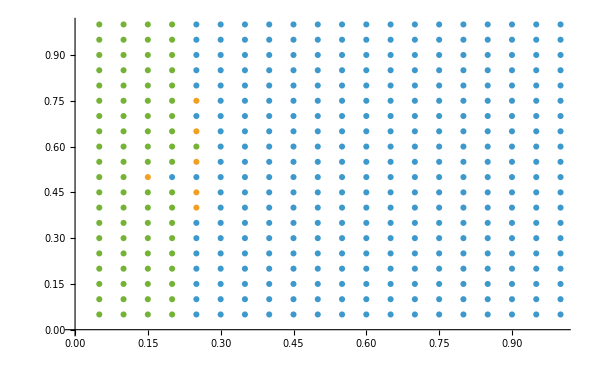

```mathematica
errorSSacc = Table[Join[evalSSacc[[i,;;2]], {-Log10[Abs[evalSSacc[[i,3]]/evalExact[[i,3]]-1]]}], {i,1,Length[evalSSacc]}];
errorColor = errorSSacc/. {a_,b_,c_ /; c<9 }-> {a,b,red}/. {a_,b_,c_ /; c>=9 && c <10}-> {a,b,blue}/. {a_,b_,c_ /; c>=10}-> {a,b,green};
awesome=Cases[errorColor, {a_,b_,green}][[;;,;;2]];
good=Cases[errorColor, {a_,b_,blue}][[;;,;;2]];
bad=Cases[errorColor, {a_,b_,red}][[;;,;;2]];
ListPlot[{awesome,good,bad}]
```

```mathematica
HERCS[3][[1]]
```

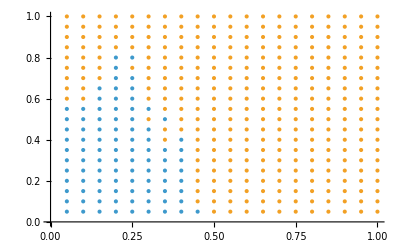

```mathematica
errorHELC = Table[Join[evalHELC[[i,;;2]], {-Log10[Abs[evalHELC[[i,3]]/evalExact[[i,3]]-1]]}], {i,1,Length[evalHELC]}];
errorColor = errorHELC/. {a_,b_,c_ /; c<10 }-> {a,b,red}/. {a_,b_,c_ /; c>=10}-> {a,b,blue};
good=Cases[errorColor, {a_,b_,blue}][[;;,;;2]];
bad=Cases[errorColor, {a_,b_,red}][[;;,;;2]];
ListPlot[{good,bad}]
```

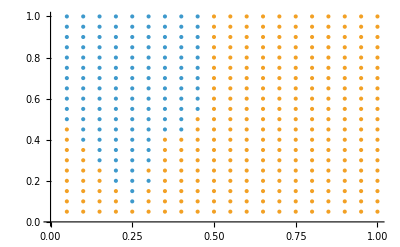

```mathematica
errorHERC = Table[Join[evalHERC[[i,;;2]], {-Log10[Abs[evalHERC[[i,3]]/evalExact[[i,3]]-1]]}], {i,1,Length[evalHERC]}];
errorColor = errorHERC/. {a_,b_,c_ /; c<10}-> {a,b,red}/. {a_,b_,c_ /; c>=10 }-> {a,b,blue};
good=Cases[errorColor, {a_,b_,blue}][[;;,;;2]];
bad=Cases[errorColor, {a_,b_,red}][[;;,;;2]];
ListPlot[{good,bad}]
```

```mathematica
(*errorHE = Table[Join[evalHE[[i,;;2]], {-Log10[Abs[evalHE[[i,3]]/evalExact[[i,3]]-1]]}], {i,1,Length[evalHE]}];
errorColor = errorHE/. {a_,b_,c_ /; c<5 }-> {a,b,red}/. {a_,b_,c_ /; c>=5 }-> {a,b,blue};
good=Cases[errorColor, {a_,b_,blue}][[;;,;;2]];
bad=Cases[errorColor, {a_,b_,red}][[;;,;;2]];
ListPlot[{good,bad}]*)
```

```mathematica
eval[point_,weight_, which_, precision_]:= Module[{z,y, toeval,pointbz ,pointLC,bz,pointt},
z = point[[1,2]];
y = point[[2,2]];
pointt =  {bz -> (1-z /. point),t-> -1/2Log[z/.point]};
pointLC = {δ-> (y+z /. point), t-> ((√z)/(√(y+z))/.point)};
pointRC = {δ-> (1-y+z /. point), t-> ((√z)/(√(1-y+z))/.point)};
If[z<0.32 && y <0.5, toeval = HELCS[weight][[which]]/.pointLC;];
If[z<0.32 && y >=0.5, toeval = HERCS[weight][[which]]/.pointRC;];
If[z>=0.32, toeval = SSt[weight][[which]]/.pointt/.point;];
Return[Ginsh[toeval, Join[point, pointt], PrecisionGoal-> precision]]
]
```

```mathematica
numpoint=20
points=Table[i, {i,1,numpoint}];
points = Table[0,{i,1,numpoint}]+points 1/numpoint-0.0001;
grid=Flatten[Table[{z-> points[[i]],y->  points[[j]]  }, {i,1,numpoint}, {j,1,numpoint}],1];
```

20

```mathematica
sol1reg[[1]]//.toZY/.bz -> 1-z /.
```

1/8 (2 G[0,√z]+4 G[0,√((y+z-y z)/(1-y+y z))]+3 G[-1/(√((y+z-y z)/(1-y+y z))),√z]+3 G[-√((y+z-y z)/(1-y+y z)),√z]-Log[4])

```mathematica
evaluated= {};
Do[evaluated= Append[evaluated,{grid[[i,1,2]],grid[[i,2,2]],eval[grid[[i]], 1,1,30]}];If[Mod[i,50]==0,Print[i]],{i,1,Length[grid]}]
evalExact= {};
Do[evalExact= Append[evalExact,{grid[[i,1,2]],grid[[i,2,2]],Ginsh[sol1reg[[1]] //.toZY/.bz-> 1-z /.grid[[i]],{},PrecisionGoal-> 30]}];If[Mod[i,50]==0,Print[i]],{i,1,Length[grid]}]
```

50

100

150

200

250

300

350

400

50

100

150

200

250

300

350

400

```mathematica
Position[errorColor,{0.5499,0.2499,Indeterminate}]
```

{{205}}

```mathematica
errorColor
```

```mathematica
evaluated[[205,3]]
evalExact[[205,3]]
Log10[Abs[evaluated[[205,3]]/evalExact[[205,3]]-1]]
```

```mathematica
Abs[evaluated[[205,3]]/evalExact[[205,3]]-1]+10^(-40)
```

1.×10^-40

```mathematica
Log10[Abs[evaluated[[i,3]]/evalExact[[i,3]]-1]]
```

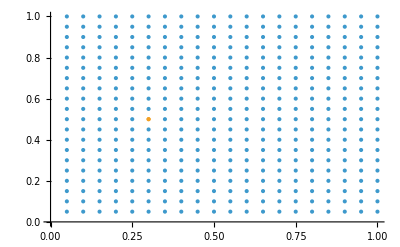

```mathematica
error = Table[Join[evaluated[[i,;;2]], {-Log10[Abs[evaluated[[i,3]]/evalExact[[i,3]]-1]+10^(-40)]}], {i,1,Length[evaluated]}];
errorColor = error/. {a_,b_,c_ /; c<11}-> {a,b,red}/. {a_,b_,c_ /; c>=11 }-> {a,b,blue};
good=Cases[errorColor, {a_,b_,blue}][[;;,;;2]];
bad=Cases[errorColor, {a_,b_,red}][[;;,;;2]];
ListPlot[{good,bad}]
```

```mathematica
error = Table[Join[evaluated[[i,;;2]], {-Log10[Abs[evaluated[[i,3]]/evalExact[[i,3]]-1]]}], {i,1,Length[evaluated]}];
```

```mathematica
ListPlot3D[error]
```

-Graphics3D-

```mathematica
ListPlot3D[{evaluated, evalExact}]
ListPlot3D[evalExact]
```

-Graphics3D-